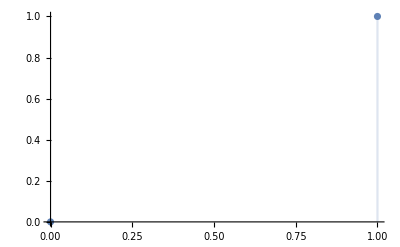

```mathematica
DiscretePlot[
x, {x, 0, 1}]
```

```mathematica
1==∫_0^a xⅆx
```

1==a^2/2

```mathematica
Reduce[1==a^2/2]
```

a==-√2||a==√2

```mathematica
Reduce[1==a^2/2&&a>0,a,Reals]
```

a==√2

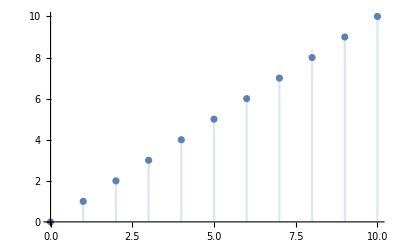

```mathematica
DiscretePlot[
x, {x, 0, 10}]
```

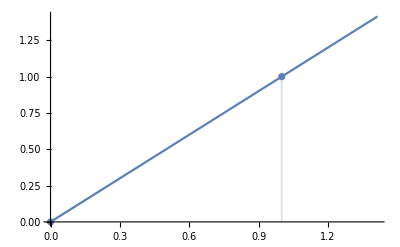

```mathematica
Show[{
Plot[x,{x,0,√2}],
DiscretePlot[x,{x,0,1}]}]
```

```mathematica
Sum[x,{x,0,2}]
```

3

```mathematica
3==∫_0^a xⅆx
```

3==a^2/2

```mathematica
Reduce[3==a^2/2&&a>0,a,Reals]
```

a==√6

```mathematica
b==∫_0^a xⅆx
```

b==a^2/2

```mathematica
Solve[b==a^2/2,a]
```

{{a→-√2 √b},{a→√2 √b}}

```mathematica
Manipulate[
Show[{
Plot[x,{x,0,√(2a)}],
ListPlot[{{a, a}}]}],
{a, 1, 10, 1}]
```

```mathematica
Sum[i,{i, 0, a}]
```

1/2 a (1+a)

```mathematica
Sum[i,{i, 0, a}]
```

1/2 a (1+a)

```mathematica
Expand[1/2 a (1+a)]
```

a/2+a^2/2

```mathematica
∫_0^a xⅆx
```

a^2/2

```mathematica
{Sum[i,{i, 0, a}], ∫_0^a xⅆx}
```

{1/2 a (1+a),a^2/2}

```mathematica
With[{f=#^2&},
{Expand[Sum[f[i],{i, 0, a}]], ∫_0^a f[i]ⅆi}]
```

{a/6+a^2/2+a^3/3,a^3/3}

```mathematica
{Expand[Sum[f[i],{i, 0, a}]], ∫_0^a f'[i]ⅆi}
```

{∑_(i=0)^a f[i],∫_0^a f'[i]ⅆi}

```mathematica
With[{f=#^3+#^2+#&},
{Expand[Sum[f[i],{i, 0, a}]], ∫_0^a f[i]ⅆi}]
```

{(2 a)/3+(5 a^2)/4+(5 a^3)/6+a^4/4,a^2/2+a^3/3+a^4/4}

```mathematica
First[%]/Last[%]
```

((2 a)/3+(5 a^2)/4+(5 a^3)/6+a^4/4)/(a^2/2+a^3/3+a^4/4)

```mathematica
FullSimplify[((2 a)/3+(5 a^2)/4+(5 a^3)/6+a^4/4)/(a^2/2+a^3/3+a^4/4)]
```

((1+a) (8+a (7+3 a)))/(a (6+a (4+3 a)))

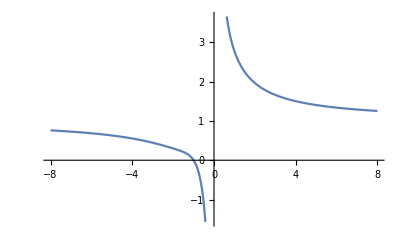

```mathematica
Plot[((1+a) (8+a (7+3 a)))/(a (6+a (4+3 a))),{a,-8,8}]
```

```mathematica
Limit[((1+a) (8+a (7+3 a)))/(a (6+a (4+3 a))), a->∞]
```

1

```mathematica
{Expand[Sum[f[i],{i, 0, a}]], ∫_0^a f[i]ⅆi}
```

{∑_(i=0)^a f[i],∫_0^a f[i]ⅆi}

```mathematica
(∑_(i=0)^a f[i])/(∫_0^a f[i]ⅆi)==1
```

(∑_(i=0)^a f[i])/(∫_0^a f[i]ⅆi)==1

```mathematica
∑_(i=0)^a f[i]==∫_0^a f[i]ⅆi+g[i]
```

∑_(i=0)^a f[i]==g[i]+∫_0^a f[i]ⅆi

```mathematica
With[{f=#^3+#^2+#&},
Sum[f[i],{i, 0, a}]-∫_0^a f[i]ⅆi]
```

-a^2/2-a^3/3-a^4/4+1/12 a (1+a) (8+7 a+3 a^2)

```mathematica
Simplify[-a^2/2-a^3/3-a^4/4+1/12 a (1+a) (8+7 a+3 a^2)]
```

1/12 a (8+9 a+6 a^2)

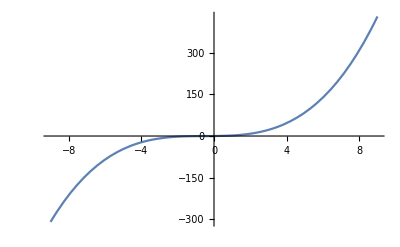

```mathematica
Plot[1/12 a (8+9 a+6 a^2),{a,-9.,9.}]
```

```mathematica
∑_(i=0)^a f[i]-g[i]==∫_0^a f[i]ⅆi
```

-g[i]+∑_(i=0)^a f[i]==∫_0^a f[i]ⅆi

```mathematica
Needs["VariationalMethods`"]
```

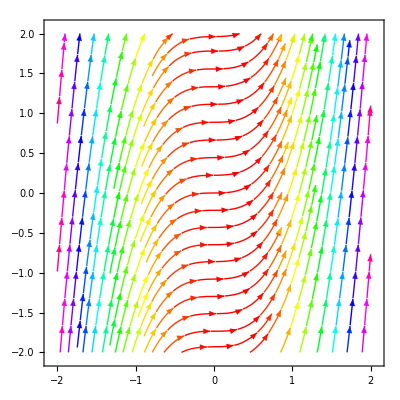

```mathematica
StreamPlot[{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}, StreamColorFunction->Hue]
```

```mathematica
StreamPlot[{1, 3 x^2}, {x, -2, 2}, {y, -2, 2}, StreamColorFunction->Hue]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1-x,1-f[x]}], Element[x|f[x],Reals]]
```

(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))
```

1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
Reduce[1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))]

```mathematica
Solve[
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
1-3 x^2+3 x^3
```

1-3 x^2+3 x^3

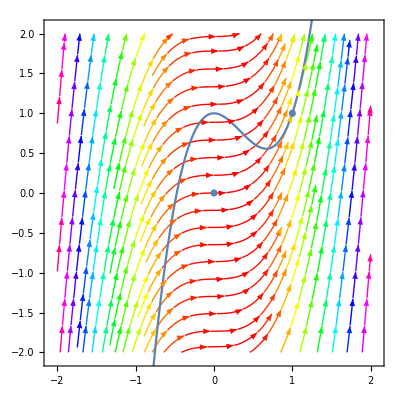

```mathematica
Show[{
StreamPlot[{1, 3 x^2},
 {x, -2, 2}, {y, -2, 2},
 StreamColorFunction->Hue],
Plot[
1-3 x^2+3 x^3, 
{x, -2, 2}],
ListPlot[{{0,0}, {1,1}}]}]
```

```mathematica
Solve[
0==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]
```

{{f[x]→(1-x+3 x^2)/(3 x^2)}}

```mathematica
(1-x+3 x^2)/(3 x^2)
```

(1-x+3 x^2)/(3 x^2)

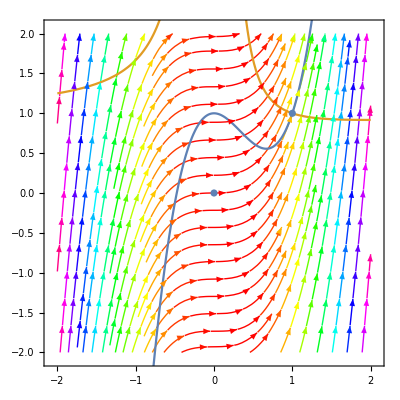

```mathematica
Show[{
StreamPlot[{1, 3 x^2},
 {x, -2, 2}, {y, -2, 2},
 StreamColorFunction->Hue],
Plot[{
1-3 x^2+3 x^3,
(1-x+3 x^2)/(3 x^2)},
{x, -2, 2}],
ListPlot[{{0,0}, {1,1}}]}]
```

```mathematica
VariationalD[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x],x]
```

-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))

```mathematica
1==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))
```

1==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))

```mathematica
Reduce[1==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[1==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))]

```mathematica
Solve[
1==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2)),f[x]]
```

{{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,1]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,2]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,3]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,4]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,5]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,6]}}

```mathematica
EulerEquations[Sqrt[1+y'[x]^2],y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
EulerEquations[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x],x]
```

-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))==0

```mathematica
Solve[
-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))==0, f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
discrete[f,x]==continue[f,x]+g[x]
```

```mathematica
facebook=ServiceConnect["Facebook","New"]
```

ServiceObject[…]

```mathematica
facebook["Picture","UserID"->6815841748]
```

-Graphics-

```mathematica
facebook["Picture"]
```

-Graphics-

```mathematica
facebook["Cover"]
```

Missing[NotAvailable]

```mathematica
facebook
```

ServiceObject[…]

```mathematica
facebook["Properties"]
```

ServiceObject::noget: The parameter Properties is not available for the service Facebook.

ServiceObject[…][Properties]

```mathematica
Element[a,Booleans]
```

a∈Booleans

```mathematica
FindInstance[a∈Booleans,{a}]
```

{{a→True}}

```mathematica
Reduce[a∈Booleans]
```

Reduce::naqs: a∈Booleans is not a quantified system of equations and inequalities.

Reduce[a∈Booleans]

```mathematica
Solve[
0==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2)),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
FullSimplify[
Normalize[D[{x, x^3},x]].
Normalize[{1-x, 1-f[x]}],Element[x|f[x],Reals]]
```

(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))
```

1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
Reduce[1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))]

```mathematica
Solve[
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
Power[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),-1]
```

(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))/(1+x (-1+3 x)-3 x^2 f[x])

```mathematica
Solve[
1==(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))/(1+x (-1+3 x)-3 x^2 f[x]),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
1==a/b
```

1==a/b

```mathematica
VariationalD[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x],x]
```

-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))

```mathematica
0==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))
```

0==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))

```mathematica
Solve[
0==-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2)),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
Solve[
0==Power[-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2)),-1],f[x]]
```

{{f[x]→1-√(-1+2 x-x^2)},{f[x]→1+√(-1+2 x-x^2)},{f[x]→(1+9 x^4-√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4)},{f[x]→(1+9 x^4+√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4)}}

```mathematica
StreamPlot[{1, 3 x^2},{x,-2,2},{y,-2,2},StreamColorFunction->Hue]
```

-Graphics-

```mathematica
{1-√(-1+2 x-x^2),1+√(-1+2 x-x^2),(1+9 x^4-√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4),(1+9 x^4+√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4)}
```

{1-√(-1+2 x-x^2),1+√(-1+2 x-x^2),(1+9 x^4-√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4),(1+9 x^4+√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4)}

```mathematica
Plot[
{1-√(-1+2 x-x^2),1+√(-1+2 x-x^2),(1+9 x^4-√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4),(1+9 x^4+√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4)},
{x,-2,2}]
```

-Graphics-

```mathematica
Plot[
(1+9 x^4+√(-1+2 x-x^2-18 x^4+36 x^5-18 x^6-81 x^8+162 x^9-81 x^10))/(1+9 x^4),
{x,-2,2}]
```

-Graphics-

```mathematica
Plot[1+√(-1+2 x-x^2),{x,-2,2}]
```

-Graphics-

```mathematica
FullSimplify[
Normalize[D[{x, x^3},x]].
Normalize[{1-x, 1-f[x]}],Element[x|f[x],Reals]]
```

(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))
```

1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))

```mathematica
Solve[
1==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
Solve[
0==(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]
```

{{f[x]→(1-x+3 x^2)/(3 x^2)}}

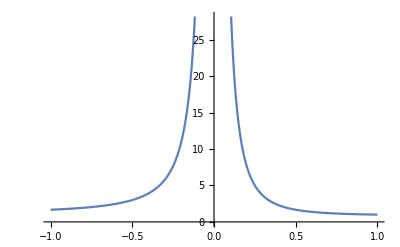

```mathematica
Plot[
(1-x+3 x^2)/(3 x^2),{x,-1,1}]
```

```mathematica
D[
(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x]]-
D[
D[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f'[x]],x]==0
```

-(3 x^2)/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))-((1+9 x^4) (-1+f[x]) (1+x (-1+3 x)-3 x^2 f[x]))/(((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))^(3/2))==0

```mathematica
Reduce[-(3 x^2)/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))-((1+9 x^4) (-1+f[x]) (1+x (-1+3 x)-3 x^2 f[x]))/(((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))^(3/2))==0]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-(3 x^2)/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))-((1+9 x^4) (-1+f[x]) (1+x (-1+3 x)-3 x^2 f[x]))/(((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))^(3/2))==0]

```mathematica
Solve[
-(3 x^2)/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2)))-((1+9 x^4) (-1+f[x]) (1+x (-1+3 x)-3 x^2 f[x]))/(((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))^(3/2))==0,f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
VariationalD[(1+x (-1+3 x)-3 x^2 f[x])/(√((1+9 x^4) ((-1+x)^2+(-1+f[x])^2))),f[x],x]
```

-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))

```mathematica
Solve[
-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))==0,f[x]]
```

{{f[x]→1-3 x^2+3 x^3}}

```mathematica
Solve[
-((-1+x) (1+9 x^4) (1-3 x^2+3 x^3-f[x]))/(((1+9 x^4) (2-2 x+x^2-2 f[x]+f[x]^2))^(3/2))==1,f[x]]
```

{{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,1]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,2]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,3]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,4]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,5]},{f[x]→Root[82-186 x+270 x^2-252 x^3+153 x^4-54 x^5+9 x^6-19/(1+9 x^4)-(12 x)/(1+9 x^4)+(99 x^2)/(1+9 x^4)-(198 x^3)/(1+9 x^4)+(-234+438 x-432 x^2+216 x^3-54 x^4+36/(1+9 x^4)-(42 x)/(1+9 x^4)-(36 x^2)/(1+9 x^4)+(162 x^3)/(1+9 x^4)) #1+(324-432 x+324 x^2-108 x^3+27 x^4-9/(1+9 x^4)+(18 x)/(1+9 x^4)-(9 x^2)/(1+9 x^4)) #1^2+(-288+216 x-108 x^2) #1^3+(162-54 x+27 x^2) #1^4-54 #1^5+9 #1^6&,6]}}

```mathematica
\[Distributed]
```

```mathematica
x\[Distributed]NormalDistribution[]
```

x\[Distributed]NormalDistribution[0,1]

```mathematica
Probability[4,x\[Distributed]NormalDistribution[0,1]]
```

Boole[4]

```mathematica
Probability[x+x,x\[Distributed]NormalDistribution[0,1]]
```

Probability[2 x,x\[Distributed]NormalDistribution[0,1]]

```mathematica
Probability[x,x\[Distributed]NormalDistribution[0,1]]
```

Probability[x,x\[Distributed]NormalDistribution[0,1]]

```mathematica
Expectation[x]
```

Expectation::argmu: Expectation called with 1 argument; 2 or more arguments are expected.

Expectation[x]

```mathematica
Expectation[x,x\[Distributed]NormalDistribution[0,1]]
```

0

```mathematica
Expectation[x,x\[Distributed]UniformDistribution[]]
```

1/2

```mathematica
Probability[x≤3,x\[Distributed]NormalDistribution[]]
```

1/2 (1+Erf[3/(√2)])

```mathematica
Probability[x==3,x\[Distributed]NormalDistribution[]]
```

0

```mathematica
RandomInteger[100,100]
```

{57,72,19,20,28,3,82,40,33,76,37,72,70,33,59,7,31,86,87,3,34,30,48,48,89,31,25,7,9,78,98,1,9,55,0,56,12,16,38,64,94,36,28,51,14,35,69,41,42,41,61,19,97,91,72,16,0,61,53,96,11,43,94,79,23,12,99,95,22,15,40,31,81,100,8,0,95,37,14,31,24,38,94,41,31,35,46,32,35,54,8,6,22,4,6,58,1,3,62,69}

```mathematica
RandomSample[Out[116], 1]
```

{72}

```mathematica
Mean[RandomSample[Out[116], 1]]
```

35

```mathematica
1==∫_-a^a x^2 ⅆx
```

1==(2 a^3)/3

```mathematica
Solve[1==(2 a^3)/3,{a}]
```

{{a→-(-3/2)^(1/3)},{a→(3/2)^(1/3)},{a→(-1)^(2/3) (3/2)^(1/3)}}

```mathematica
Reduce[1==(2 a^3)/3]
```

a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3)

```mathematica
1/2==∫_0^a x^2 ⅆx
```

1/2==a^3/3

```mathematica
Reduce[1/2==a^3/3]
```

a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3)

```mathematica
Reduce[1/2==a^3/3&&a>0,a,Reals]
```

a==(3/2)^(1/3)

```mathematica
x^2
```

x^2

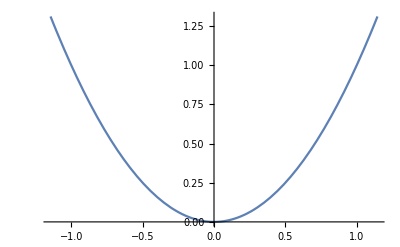

```mathematica
Plot[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]
```

```mathematica
Plot3D[
PDF[DirichletDistribution[{2,3,4}],{x,y}],
{x,0,3/5},{y,0,3/5},RegionFunction->Function[{x,y,z},x^2+y^2<1/4&&x+y<6/7],Mesh->None,PlotStyle->Opacity[0.7],Filling->Bottom]
```

-Graphics3D-

```mathematica
Mean[Range[10]]
```

11/2

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Mean[Out[131]]
```

11/2

```mathematica
Median[Out[131]]
```

11/2

```mathematica
Variance[Out[131]]
```

55/6

```mathematica
N[55/6]
```

9.16667

```mathematica
StandardDeviation[Out[131]]
```

√(55/6)

```mathematica
N[√(55/6)]
```

3.02765

```mathematica
GeometricMean[Out[131]]
```

2^(4/5) 3^(2/5) 5^(1/5) 7^(1/10)

```mathematica
N[2^(4/5) 3^(2/5) 5^(1/5) 7^(1/10)]
```

4.52873

```mathematica
4.528728688116765^2
```

20.5094

```mathematica
Sum[i, {i, Range[10]}]
```

55

```mathematica
Product[i, {i, Range[10]}]
```

3628800

```mathematica
Kurtosis[f[x]]
```

Kurtosis[f[x]]

```mathematica
Kurtosis[Out[131]]
```

293/165

```mathematica
N[293/165]
```

1.77576

```mathematica
Skewness[Out[131]]
```

0



```mathematica
CompleteGraph[1]
```



```mathematica
CompleteGraph[2]
```



```mathematica
CompleteGraph[3]
```

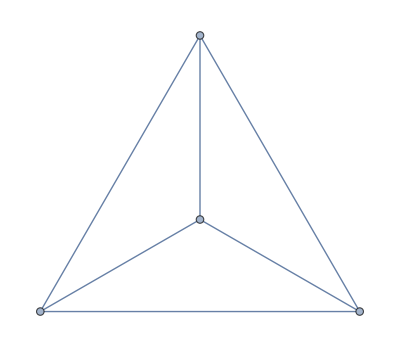

```mathematica
CompleteGraph[4]
```

CompleteGraph::ilsmp: Single or list of positive machine-sized integers expected at position 1 of CompleteGraph[0].


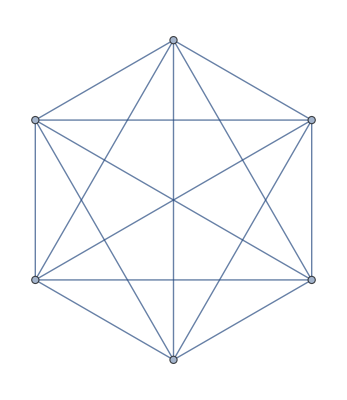
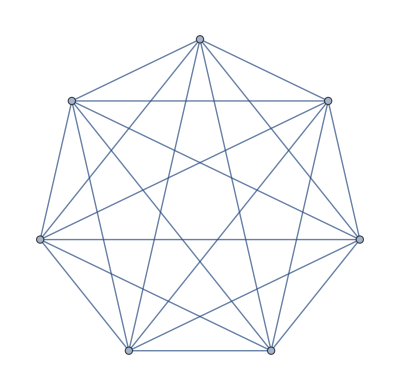
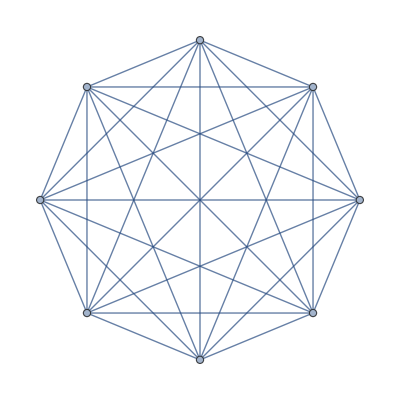
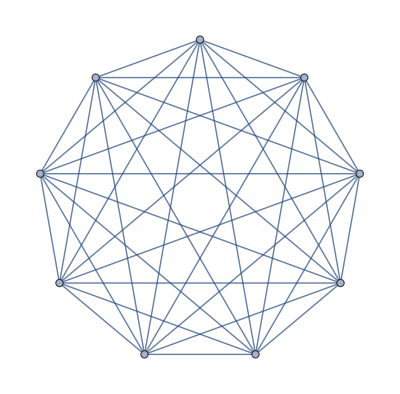
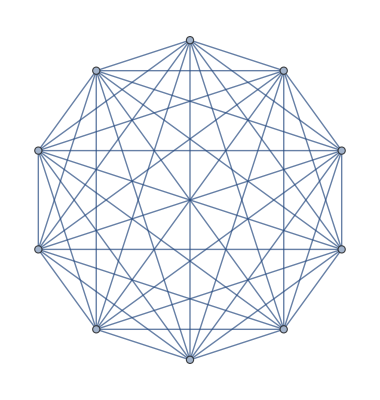
{CompleteGraph[0],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
CompleteGraph[i],{i, 0, 10}]
```

```mathematica
Table[
CompleteGraph[i],{i, 1, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

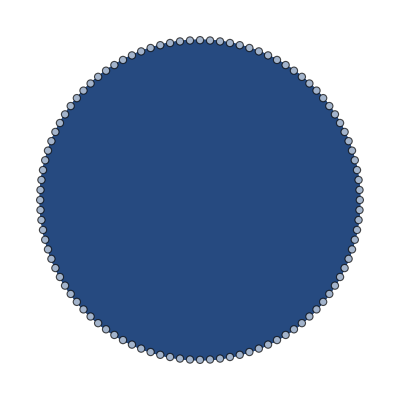

```mathematica
CompleteGraph[100]
```

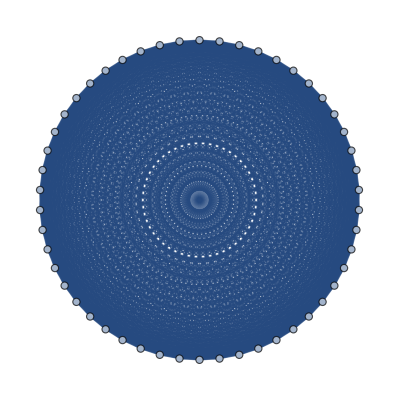

```mathematica
CompleteGraph[50]
```

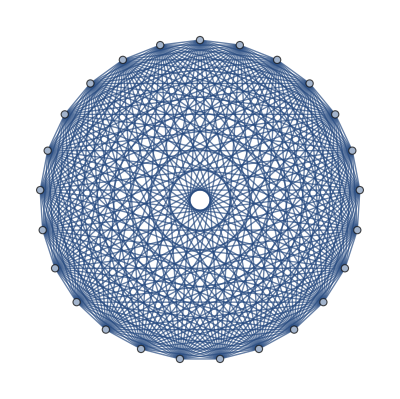

```mathematica
CompleteGraph[25]
```

```mathematica
Out[116]
```

{57,72,19,20,28,3,82,40,33,76,37,72,70,33,59,7,31,86,87,3,34,30,48,48,89,31,25,7,9,78,98,1,9,55,0,56,12,16,38,64,94,36,28,51,14,35,69,41,42,41,61,19,97,91,72,16,0,61,53,96,11,43,94,79,23,12,99,95,22,15,40,31,81,100,8,0,95,37,14,31,24,38,94,41,31,35,46,32,35,54,8,6,22,4,6,58,1,3,62,69}

```mathematica
RandomSample[Out[116]]
```

{87,98,40,94,72,100,36,6,22,32,53,4,99,64,3,94,35,6,82,51,41,38,9,0,28,61,72,70,25,69,97,31,69,8,89,1,37,57,16,0,31,96,33,78,48,28,95,1,38,37,95,61,81,35,40,76,12,22,11,94,8,3,48,24,54,56,15,35,43,9,62,0,31,42,30,20,33,31,41,19,23,7,14,31,14,3,79,58,12,59,72,34,55,86,46,41,16,91,7,19}

```mathematica
RandomSample[Out[116],1]
```

{40}

```mathematica
Mean[RandomSample[Out[116],1]]
```

37

```mathematica
Mean[Out[116]]
```

4279/100

```mathematica
N[4279/100]
```

42.79

```mathematica
Table[
N[Mean[RandomSample[Out[116],i]]], 
{i, 1,Length[Out[116]]}]
```

{69.,56.5,26.6667,32.5,46.4,18.5,44.,41.25,42.2222,44.,45.1818,42.6667,35.6923,37.2857,32.,38.0625,44.7059,60.4444,38.8421,42.25,46.5714,51.,46.2609,47.8333,49.08,44.4615,41.2222,43.4286,43.7241,40.9333,40.1613,45.1875,44.303,45.5294,41.8571,48.0278,42.4054,46.6053,41.0513,41.275,43.7317,41.7381,42.,42.8636,44.4667,41.8696,38.1064,39.8125,43.6122,41.56,40.5686,45.8846,37.6981,43.1667,36.6182,44.2143,41.4211,45.0172,48.3559,42.85,42.7213,43.9677,39.5238,43.4375,47.8923,44.2879,44.8657,43.25,40.6087,40.3429,45.6901,38.1806,41.6301,43.4865,42.64,42.2895,42.1039,44.5256,42.557,43.25,43.9506,43.6707,43.8916,45.9048,41.8588,43.6279,43.2299,41.9886,42.1348,43.2556,44.044,41.0761,42.4516,41.4043,44.0947,43.4583,43.0825,42.3571,43.1313,42.79}

```mathematica
Table[
{i, N[Mean[RandomSample[Out[116],i]]]}, 
{i, 1,Length[Out[116]]}]
```

{{1,6.},{2,33.5},{3,23.},{4,41.5},{5,50.},{6,34.3333},{7,55.2857},{8,29.5},{9,24.7778},{10,42.6},{11,39.5455},{12,28.9167},{13,50.8462},{14,34.6429},{15,49.3333},{16,44.4375},{17,38.7059},{18,43.2778},{19,45.8947},{20,40.95},{21,41.1905},{22,42.4545},{23,34.087},{24,54.875},{25,46.04},{26,35.6154},{27,37.3704},{28,41.2143},{29,41.1379},{30,46.2},{31,38.0323},{32,47.6875},{33,41.4242},{34,44.5294},{35,43.3429},{36,37.9722},{37,36.},{38,39.6842},{39,42.8718},{40,35.775},{41,43.9024},{42,53.0952},{43,45.5814},{44,40.8636},{45,41.8667},{46,37.6739},{47,43.2766},{48,46.6667},{49,43.1224},{50,45.06},{51,39.7451},{52,40.7308},{53,38.6792},{54,42.2407},{55,41.6364},{56,39.3393},{57,40.4386},{58,41.3793},{59,36.6271},{60,48.1833},{61,40.918},{62,41.5484},{63,41.5714},{64,44.25},{65,46.2923},{66,40.3485},{67,40.0299},{68,43.5441},{69,42.1594},{70,40.3},{71,46.507},{72,42.8056},{73,39.3836},{74,45.},{75,43.4533},{76,42.3026},{77,44.013},{78,42.6667},{79,44.2532},{80,41.3625},{81,43.1235},{82,39.8049},{83,44.0843},{84,41.4405},{85,44.0353},{86,41.8488},{87,42.5747},{88,41.9432},{89,42.9888},{90,41.3778},{91,41.8352},{92,43.3587},{93,43.0323},{94,43.5},{95,42.5158},{96,42.1354},{97,42.7835},{98,42.3878},{99,43.1111},{100,42.79}}

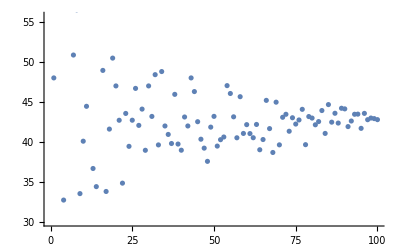

```mathematica
ListPlot[Table[
{i, N[Mean[RandomSample[Out[116],i]]]}, 
{i, 1,Length[Out[116]]}] ]
```

```mathematica
RandomInteger[10000,1000]
```

{91,5879,2645,1105,557,2271,344,8582,8009,3911,539,7504,931,4297,5257,1505,4040,6276,4459,2852,5869,7321,449,5723,4007,463,8046,8819,4520,8201,6259,3808,7224,6894,1814,3351,942,6761,218,9519,6949,6528,2310,4500,8321,4793,9120,5682,6574,2843,9278,7206,7654,8769,9027,4579,2057,2876,9185,9679,6253,7142,6130,6397,5228,1786,1716,2076,4878,5120,4041,1377,8127,3430,8769,678,5961,2078,6670,7002,8214,2636,4473,7534,484,9303,5456,6201,7762,8032,6600,1461,5864,8151,6149,7654,4864,3007,9059,1907,2447,8114,9012,8856,3415,7463,635,3772,8152,3525,5781,6345,9407,3456,9544,9341,703,8033,807,8301,3042,7208,3894,4487,1069,4782,4298,8255,2866,153,5292,625,3803,1448,1488,9625,5049,874,4602,437,9146,9280,831,8193,4546,9205,4541,3448,9731,7929,298,1993,7057,2695,4884,1772,146,3892,2841,1753,423,1112,3749,1536,1654,4114,9228,2979,6482,5339,1195,5953,9614,1812,5144,8777,9901,4122,1379,2862,3773,9568,220,356,9803,566,8008,4537,2314,6085,1564,8080,1197,897,4671,1218,7294,4494,3109,7941,11,907,4342,4694,937,1332,2111,851,4007,4863,7440,2057,9594,4612,1249,8383,4668,1782,9254,9359,1597,4147,5821,339,3041,5566,1967,8970,5306,8143,8795,7170,612,7391,977,8634,119,7154,431,195,8159,1319,419,444,8918,7971,2591,7054,9273,9738,3951,200,5756,8951,9626,7710,4689,7154,3227,9093,5238,9453,1248,981,4750,7795,5049,7222,2053,8137,6267,1721,6,106,4193,5816,9145,1691,2336,327,8849,8351,5861,5201,5625,6018,8660,2942,2069,8080,2192,8423,39,5495,3052,3289,142,9307,9843,8000,6599,9263,734,9200,7431,7107,6358,7545,6202,2063,3718,7217,1150,4463,7996,5227,7751,4717,7675,3443,929,2979,1897,6461,7453,1217,9898,7597,1827,5178,5346,5786,6995,8460,8950,41,9123,6098,1499,7608,836,994,1805,824,9693,1438,5634,2636,1690,9194,4061,9301,3233,4233,7454,8888,8811,4619,1920,8709,9280,6591,3225,8917,2249,229,6243,461,5933,9079,9816,5864,3827,564,2522,1847,9966,6460,1439,2691,6152,3515,5562,6615,3433,6566,3460,8447,733,327,134,605,105,2006,7016,5766,8507,7512,4106,3289,6647,1993,3336,7937,8940,9811,4175,879,8145,9086,3280,7589,1072,550,1359,95,4970,8188,288,2854,9594,1509,1984,7988,988,6367,6081,2409,7339,11,23,1338,1916,328,3225,5675,3830,524,2404,2626,8487,7696,2384,2495,5044,434,5007,8778,9931,9744,7687,9758,2948,568,7972,9994,6231,6461,2809,1601,2068,3431,7554,8868,5799,755,1145,3619,8040,5539,6096,2685,1300,3209,6221,5504,6931,8120,3138,1175,9682,4019,3520,6129,2965,9246,317,425,3680,92,8079,9110,7442,7106,5899,1780,8326,3258,3150,4585,2714,9401,1302,6513,9183,1684,5438,7650,4941,9364,9359,1898,2558,8268,6925,7876,8450,2344,8750,538,9879,4696,4533,140,7423,7262,1275,8811,5136,1840,3859,796,5543,5564,9955,7558,1718,3207,7996,2023,7832,4590,4771,3945,7828,596,8004,3477,5815,4619,1823,5555,574,9965,7957,6304,2432,7509,1263,7359,8539,5785,6873,2186,7654,4120,7890,1004,4504,2604,8689,554,9761,5681,7330,4405,8320,8883,6083,2614,2594,9554,1351,1452,7295,7616,1257,8018,5590,3856,6226,8848,7165,6349,8022,1287,7650,4468,3922,9266,2933,4608,8790,7476,5607,2852,1341,6610,4335,1648,8513,8415,1692,4167,8033,6310,7393,7783,6581,518,1205,8354,7601,3438,3136,2852,7760,2420,7872,1743,9438,739,3712,7175,4415,8107,9699,5258,2195,209,2929,3710,2244,2638,6081,8845,3662,9247,2135,3302,2241,848,6457,8156,577,7889,6308,7573,8481,4855,6607,7678,133,690,6438,5486,6468,9857,3397,4590,9243,733,30,3722,92,8189,2741,9557,6243,9346,4794,5568,5218,1118,5318,9651,1659,8043,6696,5775,1076,6105,7558,5044,6832,4448,4009,564,801,7152,8027,3713,3631,9575,308,7228,6981,2387,6248,8649,3051,1535,2452,1205,9956,1634,8891,5852,2543,7334,8267,4758,2043,9399,9690,5788,1072,4418,6387,3374,6952,3118,8714,1014,4147,1454,9589,9008,6563,2119,6644,218,1726,8341,8337,4866,1689,8667,7723,4116,6078,9539,263,8960,9203,5650,8688,776,7362,6153,5265,4301,2436,6614,5310,7285,4503,8533,4900,2649,2833,8576,5028,6494,8559,2467,2954,2173,9013,4489,8093,1300,4355,5296,234,6005,4449,1188,7822,4944,711,1509,2757,2252,4514,2333,8580,2617,1205,2473,532,9957,1819,7351,8039,9540,6112,2174,1565,8627,8089,4026,74,3388,5566,411,9344,2292,6155,5749,4259,492,2834,5511,4335,7294,393,8674,5638,2949,7177,6977,817,5019,6259,2640,6970,4230,1707,2357,1038,1419,1215,163,7077,8056,3214,9168,7317,5460,6725,8000,6990,6424,5030,1097,3274,7202,2689,6322,6869,3526,3326,1675,6191,242,1565,6733,2707,7932,1924,6858,2748,216,2786,5785,8597,6257,5405,2384,7257,1400,912,3224,2771,7957,8137,7453,4267,85,5822,8927,95,8201,8245,289,839,9677,884,2443,5434,3289,7009,4811,1797,4527,3480,2537,9600,4281,9283,5937,6879,6748,9889,1761,2406,6862,8744,9013,4146,8364,9186,6806,9928,5541,4279,9006,6658,9917,5705,3429,9536,9414,1995,3962,8933,4020,1815,6621,2087,2331,7709,4542,5832,1728,1492,6459,5708,9708,7688,3214,1592,713,1348,9654,9270,2301,113,7605,6686,1602,7794,1739,4044,8904,1155,5329,7694,9124,3778,2323,5006,3190,4550,1452,2015,1694,8754,402,3807,4130,9686,1359,6611,8361,1217,8708,6738,3641,1319,2562,9736,5643,2584,8038,8525,3967,7001,8719}

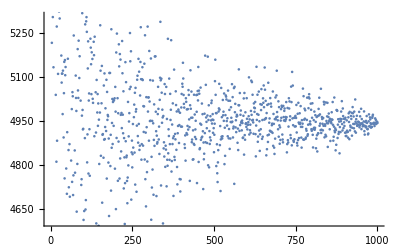

```mathematica
ListPlot[Table[
{i, N[Mean[RandomSample[Out[167],i]]]}, 
{i, 1,Length[Out[167]]}] ]
```

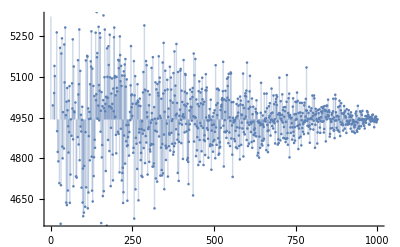

```mathematica
ListPlot[Table[
{i, N[Mean[RandomSample[Out[167],i]]]}, 
{i, 1,Length[Out[167]]}], Filling->Mean[Out[167]]]
```

```mathematica
Mean[Out[167]]
```

4942971/1000

```mathematica
N[4942971/1000]
```

4942.97

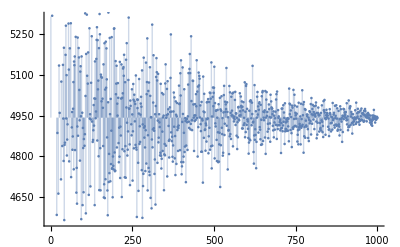

```mathematica
ListPlot[Table[
{i, N[Mean[RandomSample[Out[167],i]]]}, 
{i, 1,Length[Out[167]]}], Filling->Mean[Out[167]]]
```

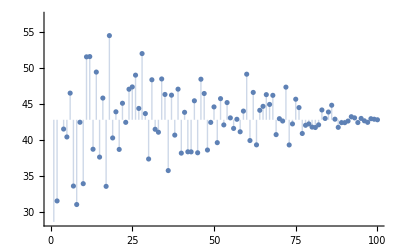

```mathematica
ListPlot[Table[
{i, N[Mean[RandomSample[Out[116],i]]]}, 
{i, 1,Length[Out[116]]}], Filling->Mean[Out[116]]]
```

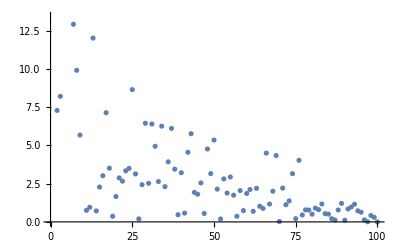

```mathematica
ListPlot[Table[
{i, Abs[Mean[Out[116]]-N[Mean[RandomSample[Out[116],i]]]]}, 
{i, 1,Length[Out[116]]}]]
```

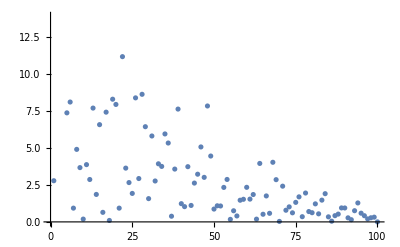
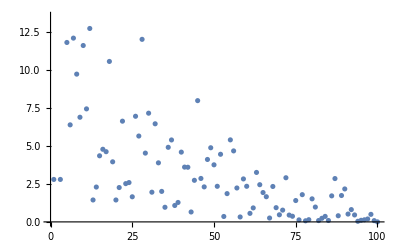

```mathematica
{ListPlot[Table[
{i, Abs[Mean[Out[116]]-N[Mean[RandomSample[Out[116],i]]]]}, 
{i, 1,Length[Out[116]]}]],ListPlot[Table[
{i, Abs[Mean[Out[116]]-N[Mean[RandomSample[Out[116],i]]]]}, 
{i, 1,Length[Out[116]]}]]}
```

```mathematica
Mean@{a,b,c}
```

1/3 (a+b+c)

```mathematica
GeometricMean@{a,b,c}
```

(a b c)^(1/3)

```mathematica
Variance@{a,b,c}
```

1/6 ((2 a-b-c) Conjugate[a]+(-a+2 b-c) Conjugate[b]+(-a-b+2 c) Conjugate[c])

```mathematica
FullSimplify[
Variance@{a,b,c}, Element[a|b|c,Reals]]
```

1/3 (a^2+b^2-b c+c^2-a (b+c))

```mathematica
FullSimplify[
StandardDeviation@{a,b,c}, Element[a|b|c,Reals]]
```

(√(a^2+b^2-b c+c^2-a (b+c)))/(√3)

```mathematica
FullSimplify[
Kurtosis@{a,b,c}, Element[a|b|c,Reals]]
```

3/2

```mathematica
FullSimplify[
Skewness@{a,b,c}, Element[a|b|c,Reals]]
```

((a+b-2 c) (2 a-b-c) (a-2 b+c))/(2 √2 (a^2+b^2-b c+c^2-a (b+c))^(3/2))

```mathematica
a[n]==a[n-1]a[n-2]
```

a[n]==a[-2+n] a[-1+n]

```mathematica
FindInstance[a[n]==a[-2+n] a[-1+n],{n}]
```

FindInstance[a[n]==a[-2+n] a[-1+n],{n}]

```mathematica
Reduce[a[n]==a[-2+n] a[-1+n]]
```

(a[n]==0&&a[-1+n]==0)||(a[-1+n]≠0&&a[-2+n]==a[n]/a[-1+n])

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==2}, a[n],n]
```

{{a[n]→2^(-Fibonacci[n]/2+LucasL[n]/2)}}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==a}, a[n],n]
```

RSolve[{a[n]==a[-2+n] a[-1+n],a[1]==1,a[2]==a},a[n],n]

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[3]==a}, a[n],n]
```

RSolve[{a[n]==a[-2+n] a[-1+n],a[1]==1,a[3]==a},a[n],n]

```mathematica
Table[{i, j}, {i, 1, 5}, {j, 1, 5}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==2}, a[n],n]
```

```mathematica
Table[
i->RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==i}, a[n],n]
, {i, 1, 9}]
```

{1→{{a[n]→1}},2→{{a[n]→2^(-Fibonacci[n]/2+LucasL[n]/2)}},3→{{a[n]→3^(-Fibonacci[n]/2+LucasL[n]/2)}},4→{{a[n]→2^(-Fibonacci[n]+LucasL[n])}},5→{{a[n]→5^(-Fibonacci[n]/2+LucasL[n]/2)}},6→{{a[n]→6^(-Fibonacci[n]/2+LucasL[n]/2)}},7→{{a[n]→7^(-Fibonacci[n]/2+LucasL[n]/2)}},8→{{a[n]→2^(-(3 Fibonacci[n])/2+(3 LucasL[n])/2)}},9→{{a[n]→3^(-Fibonacci[n]+LucasL[n])}}}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==2}, a[n],n]
```

{{a[n]→2^(-Fibonacci[n]/2+LucasL[n]/2)}}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==2,a[2]==1}, a[n],n]
```

{{a[n]→2^((3 Fibonacci[n])/2-LucasL[n]/2)}}

```mathematica
With[{b=3},{
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==b}, a[n],n],
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==1}, a[n],n]
}]
```

{{{a[n]→3^(-Fibonacci[n]/2+LucasL[n]/2)}},{{a[n]→3^((3 Fibonacci[n])/2-LucasL[n]/2)}}}

```mathematica
a[n]/.{{{a[n]->3^(-Fibonacci[n]/2+LucasL[n]/2)}},{{a[n]->3^((3 Fibonacci[n])/2-LucasL[n]/2)}}}
```

{{3^(-Fibonacci[n]/2+LucasL[n]/2)},{3^((3 Fibonacci[n])/2-LucasL[n]/2)}}

```mathematica
Flatten[{{3^(-Fibonacci[n]/2+LucasL[n]/2)},{3^((3 Fibonacci[n])/2-LucasL[n]/2)}}]
```

{3^(-Fibonacci[n]/2+LucasL[n]/2),3^((3 Fibonacci[n])/2-LucasL[n]/2)}

```mathematica
a[n]/.With[{b=3},{
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==b}, a[n],n],
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==1}, a[n],n]
}]
```

{{3^(-Fibonacci[n]/2+LucasL[n]/2)},{3^((3 Fibonacci[n])/2-LucasL[n]/2)}}

```mathematica
Flatten[
a[n]/.With[{b=3},{
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==b}, a[n],n],
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==1}, a[n],n]
}],1]
```

{3^(-Fibonacci[n]/2+LucasL[n]/2),3^((3 Fibonacci[n])/2-LucasL[n]/2)}

```mathematica
Flatten[
a[n]/.{
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==1,a[2]==b}, a[n],n],
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==1}, a[n],n]
},1]
```

{b^(-Fibonacci[n]/2+LucasL[n]/2),b^((3 Fibonacci[n])/2-LucasL[n]/2)}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==1}, a[n],n]
```

{{a[n]→b^((3 Fibonacci[n])/2-LucasL[n]/2)}}

```mathematica
RSolve[{a[n]==a[-2+n] a[-1+n], a[1]==b,a[2]==c}, a[n],n]
```

{{a[n]→ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])}}

```mathematica
Flatten[
a[n]/.{{a[n]->ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])}},1]
```

{ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])}

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])/.{b->1,c->2}
```

ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])

```mathematica
FullSimplify[ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])]
```

2^(1/2 (-Fibonacci[n]+LucasL[n]))

```mathematica
Exp[Log[a]]
```

a

```mathematica
ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])
```

ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])

```mathematica
ⅇ^(Log[2]/2(- Fibonacci[n]+LucasL[n]))
```

2^(1/2 (-Fibonacci[n]+LucasL[n]))

```mathematica
Exp[Log[2]/2]
```

√2

```mathematica
Exp[Log[2]]^(1/2)
```

√2

```mathematica
Exp[Log[a]]^(1/2)==a^(1/2)
```

True

```mathematica
ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])
```

ⅇ^(-1/2 Fibonacci[n] Log[2]+1/2 Log[2] LucasL[n])

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])
```

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])->√(ⅇ^(Fibonacci[n] (3 Log[b]-Log[c])+(-Log[b]+Log[c]) LucasL[n]))
```

ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])→√(ⅇ^(Fibonacci[n] (3 Log[b]-Log[c])+(-Log[b]+Log[c]) LucasL[n]))

```mathematica
a^(c d)==(a^c)^d
```

a^(c d)==(a^c)^d

```mathematica
FindInstance[a^(c d)==(a^c)^d,{a,c,d}]
```

{{a→68/5-(506 ⅈ)/5,c→-548/5-(168 ⅈ)/5,d→516/5-(401 ⅈ)/5}}

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])
```

ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])

```mathematica
FullSimplify[ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])]
```

ⅇ^(1/2 (Fibonacci[n] (3 Log[b]-Log[c])+(-Log[b]+Log[c]) LucasL[n]))

```mathematica
ⅇ^(1/2 (Fibonacci[n] (3 Log[b]-Log[c])(-Log[b]+Log[c]) LucasL[n]))
```

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c]))Exp[1/2 (-Log[b]+Log[c]) LucasL[n]]
```

ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])

```mathematica
√(ⅇ^(Fibonacci[n] (3 Log[b]-Log[c])))√(ⅇ^((-Log[b]+Log[c]) LucasL[n]))
```

√(ⅇ^(Fibonacci[n] (3 Log[b]-Log[c]))) √(ⅇ^((-Log[b]+Log[c]) LucasL[n]))

```mathematica
√(ⅇ^(3Fibonacci[n]Log[b])/ⅇ^(Fibonacci[n]Log[c])) √(ⅇ^((-Log[b]+Log[c]) LucasL[n]))
```

```mathematica
x^2
```

x^2

```mathematica
√(x^2)
```

√(x^2)

```mathematica
1-1
```

0

```mathematica
Hold[1-1]
```

Hold[1-1]

```mathematica
√(ⅇ^(3Fibonacci[n]Log[b])/ⅇ^(Fibonacci[n]Log[c])) √(ⅇ^((-Log[b]+Log[c]) LucasL[n]))==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])
```

√(b^(3 Fibonacci[n]) c^(-Fibonacci[n])) √(ⅇ^((-Log[b]+Log[c]) LucasL[n]))==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])

```mathematica
Reduce[√(b^(3 Fibonacci[n]) c^(-Fibonacci[n])) √(ⅇ^((-Log[b]+Log[c]) LucasL[n]))==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])]
```

(0==-√(b^(3 Fibonacci[n])) √(c^(-Fibonacci[n]))-√(b^(3 Fibonacci[n]) c^(-Fibonacci[n]))&&ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])==0&&ⅇ^((-Log[b]+Log[c]) LucasL[n])==0)||(0==√(b^(3 Fibonacci[n])) √(c^(-Fibonacci[n]))-√(b^(3 Fibonacci[n]) c^(-Fibonacci[n]))&&ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])==0&&ⅇ^((-Log[b]+Log[c]) LucasL[n])==0)||(√(ⅇ^((-Log[b]+Log[c]) LucasL[n]))≠0&&ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])==0&&c^(-Fibonacci[n])==0)||(c^(-Fibonacci[n]) ⅇ^((-Log[b]+Log[c]) LucasL[n])≠0&&√(ⅇ^((-Log[b]+Log[c]) LucasL[n]))≠0&&0==(ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])-√(ⅇ^(Fibonacci[n] (3 Log[b]-Log[c]))) √(ⅇ^((-Log[b]+Log[c]) LucasL[n])))/(√(ⅇ^((-Log[b]+Log[c]) LucasL[n])))&&b^(3 Fibonacci[n])==c^Fibonacci[n] ⅇ^(Fibonacci[n] (3 Log[b]-Log[c])))

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]))
```

ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]))

```mathematica
FullSimplify[ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]))]
```

$Aborted

```mathematica
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])==ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])
```

True

```mathematica
{ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])}
```

{ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n])}

```mathematica
{ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]),
Map[Composition[f,g],{a,b,c}]}
```

{ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]),{f[g[a]],f[g[b]],f[g[c]]}}

```mathematica
FullSimplify[
ⅇ^(1/2 Fibonacci[n] (3 Log[b]-Log[c])+1/2 (-Log[b]+Log[c]) LucasL[n]),
And[Element[n|b|c,Integers],
n>0,10>b≥1,10>c≥1,
Not[And[b==1,c==1]]]]
```

(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)

```mathematica
PowerExpand[(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)]
```

b^((3 Fibonacci[n])/2-LucasL[n]/2) c^(-Fibonacci[n]/2+LucasL[n]/2)

```mathematica
(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)
```

(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)

```mathematica
(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)==√((b^3/c)^Fibonacci[n] (c/b)^LucasL[n])
```

(b^3/c)^(Fibonacci[n]/2) (c/b)^(LucasL[n]/2)==√((b^3/c)^Fibonacci[n] (c/b)^LucasL[n])

```mathematica
√((b^3/c)^((LucasL[n] Fibonacci[n]^2)/(LucasL[n]Fibonacci[n])) (c/b)^((LucasL[n]^2 Fibonacci[n])/(LucasL[n]Fibonacci[n])))
```

√((b^3/c)^Fibonacci[n] (c/b)^LucasL[n])

```mathematica
a[n]==Piecewise[{{1, EvenQ[n]}, {0, Not[EvenQ[n]]}}]
```

a[n]==0

```mathematica
a[n]==Piecewise[{{1, EvenQ[n]}, {0, OddQ[n]}}]
```

a[n]==0

```mathematica
Solve[a[n]==0&&n∈Integers,{n}]
```

Solve[a[n]==0&&n∈ℤ,{n}]

```mathematica
FindInstance[a[n]==0,{n}]
```

FindInstance[a[n]==0,{n}]

```mathematica
a[n]==Piecewise[{{0, n==0}, {1, n==1}, {a[n-1]+a[n-2], n>1}}]
```

a[n]==(Piecewise[{{0, n==0}, {1, n==1}, {a[-2+n]+a[-1+n], n>1}, {0, True}}])

```mathematica
a[n_Integer]:=Piecewise[{{0, n==0}, {1, n==1}, {a[n-1]+a[n-2], n>1}}]
```

```mathematica
a[0]
```

0

```mathematica
a[1]
```

1

```mathematica
a[10]
```

55

```mathematica
a[10000]
```

$Aborted

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{0, n==0}, {1, n==1}, {a[n-1]+a[n-2], n>1}}]
```

```mathematica
a[100]
```

354224848179261915075

```mathematica
a[1000]
```

17147923024004226122738827244577811616833011594238408929354842393259173960805130470788839689695398991424680 Hold[a[489-1]+a[489-2]]+27745922289305716855338470916082815029348872029647830861914852073402148308000613611082094085891168867554589 Hold[a[490-1]+a[490-2]]

```mathematica
a[10000]
```

17147923024004226122738827244577811616833011594238408929354842393259173960805130470788839689695398991424680 Hold[a[9489-1]+a[9489-2]]+27745922289305716855338470916082815029348872029647830861914852073402148308000613611082094085891168867554589 Hold[a[9490-1]+a[9490-2]]

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==0}, {a[n-1]+a[n-2]+1, n>0}}]
```

```mathematica
a[0]
```

1

```mathematica
a[10]
```

232

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==0}, {a[n-1]+1, n>0}}]
```

```mathematica
a[0]
```

1

```mathematica
a[10]
```

11

```mathematica
a[100]
```

101

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], a[n-1]<10}}]
```

```mathematica
a[1]
```

1

```mathematica
a[2]
```

2

```mathematica
a[3]
```

2

```mathematica
a[4]
```

4

```mathematica
a[5]
```

8

```mathematica
Table[a[i],{i, 1, 10}]
```

{1,2,2,4,8,32,0,0,0,0}

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], a[n-1]<10}, {a Floor[a/10]-10 Floor[a/10]^2, a[n-1]≥10}}]
```

```mathematica
43/10
```

43/10

```mathematica
N[43/10]
```

4.3

```mathematica
Floor[43/10](43-10Floor[43/10])
```

12

```mathematica
Floor[a/10](a-10Floor[a/10])
```

(a-10 Floor[a/10]) Floor[a/10]

```mathematica
FullSimplify[
Floor[a/10](a-10Floor[a/10]), 
And[Element[a,Integers], 10≤a≤81]]
```

(a-10 Floor[a/10]) Floor[a/10]

```mathematica
Expand[(a-10 Floor[a/10]) Floor[a/10]]
```

a Floor[a/10]-10 Floor[a/10]^2

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], a[n-1]<10}, {a[n-1] Floor[a[n-1]/10]-10 Floor[a[n-1]/10]^2, a[n-1]≥10}}]
```

```mathematica
a[1]
```

1

```mathematica
a[2]
```

2

```mathematica
a[3]
```

2

```mathematica
a[4]
```

4

```mathematica
a[5]
```

8

```mathematica
Table[a[i], {i, 1, 20}]
```

{1,2,2,4,8,32,6,192,38,24,8,192,38,24,8,192,38,24,8,192}

```mathematica
a[n]
```

a[n]

```mathematica
FullSimplify[a[n]]
```

a[n]

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], a[n-1]<10}, {□, □}, {a[n-1] Floor[a[n-1]/10]-10 Floor[a[n-1]/10]^2, a[n-1]≥10}}]
```

```mathematica
extract10s[n_Integer]:=10Floor[n/10]
```

```mathematica
extract10s[43]
```

40

```mathematica
extract10s[n_Integer;11≤n≤81]:=10Floor[n/10]
```

```mathematica
extract10s[13]
```

10

```mathematica
extract10s[9]
```

0

```mathematica
extract10s[43]
```

40

```mathematica
extract1s[n_Integer;11≤n≤81]:=10Floor[n/10]
```

```mathematica
tens[n_Integer;11≤n≤81]:=10Floor[n/10]
```

```mathematica
ones[n_Integer;11≤n≤81]:=10Floor[n/10]
```

```mathematica
tens[4]
```

tens[4]

```mathematica
ones[n_Integer;11≤n≤81]:=n-tens[n]
```

```mathematica
Clear[tens]
```

```mathematica
tens[n_Integer;10≤n≤81]:=10Floor[n/10]
```

```mathematica
Clear[ones]
```

```mathematica
ones[n_Integer;10≤n≤81]:=n-tens[n]
```

```mathematica
ones[43]
```

ones[43]

```mathematica
tens[43]
```

tens[43]

```mathematica
Clear[ones]
```

```mathematica
tens[n_Integer]:=10Floor[n/10]
```

```mathematica
ones[n_Integer]:=Piecewise[{{n, n<10}, {n-tens[n], n≥10}}]
```

```mathematica
tens[15]
```

10

```mathematica
tens[94]
```

90

```mathematica
ones[32]
```

2

```mathematica
ones[53]
```

3

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
a[1]
```

1

```mathematica
a[2]
```

2

```mathematica
a[3]
```

2

```mathematica
Table[a[i],{i,1,10}]
```

{1,2,2,4,8,32,60,0,0,0}

```mathematica
Clear[tens]
```

```mathematica
tens[n_Integer]:=Floor[n/10]
```

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
Table[a[i],{i,1,10}]
```

{1,2,2,4,8,32,87,0,0,0}

```mathematica
tens[32]
```

3

```mathematica
ones[32]
```

29

```mathematica
Clear[ones]
```

```mathematica
ones[n_Integer]:=Piecewise[{{n, n<10}, {n-10tens[n], n≥10}}]
```

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
Table[a[i],{i,1,10}]
```

{1,2,2,4,8,32,6,12,2,4}

```mathematica
Table[a[i],{i,1,50}]
```

{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12}

```mathematica
RSolve[{a[n]},a[n],n]
```

RSolve[{a[n]},a[n],n]

```mathematica
b[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {2, n==2}, {b[n-1]b[n-2], 0≤b[n-1]<10&&0≤b[n-2]<10}, {b[n-1]ones[b[n-2]], 0≤b[n-1]<10&&81≥b[n-2]≥10}, {tens[b[n-1]]ones[b[n-1]], 81≥b[n-1]≥10}}]
```

```mathematica
Clear[b]
```

```mathematica
b[n_Integer]:=b[n]=Piecewise[{{1, n==1}, {2, n==2}, {b[n-1]b[n-2], 0≤b[n-1]<10&&0≤b[n-2]<10}, {b[n-1]ones[b[n-2]], 0≤b[n-1]<10&&81≥b[n-2]≥10}, {tens[b[n-1]]ones[b[n-1]], 81≥b[n-1]≥10}}]
```

```mathematica
Clear[b]
```

```mathematica
b[n_Integer]:=b[n]=Piecewise[{{c, n==1}, {d, n==2}, {b[n-1]b[n-2], 0≤b[n-1]<10&&0≤b[n-2]<10}, {b[n-1]ones[b[n-2]], 0≤b[n-1]<10&&81≥b[n-2]≥10}, {tens[b[n-1]]ones[b[n-1]], 81≥b[n-1]≥10}}]
```

```mathematica
b[1]
```

c

```mathematica
b[2]
```

d

```mathematica
b[3]
```

Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}]

```mathematica
b[4]
```

Piecewise[{{d (Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}]), 0≤(Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}])<10&&0≤d<10}, {ones[d] (Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}]), 0≤(Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}])<10&&81≥d≥10}, {ones[Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}]] tens[Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}]], 81≥(Piecewise[{{c d, 0≤d<10&&0≤c<10}, {d ones[c], 0≤d<10&&81≥c≥10}, {ones[d] tens[d], 81≥d≥10}, {0, True}}])≥10}, {0, True}}]

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{2, n==1}, {1, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
Table[a[i], {i, 1, 10}]
```

{2,1,2,2,4,8,32,6,12,2}

```mathematica
{1,2,2,4,8,32,6,12,2,4}
```

{1,2,2,4,8,32,6,12,2,4}

```mathematica
Clear[a]
```

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {c, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
a[2]
```

c

```mathematica
a[3]
```

Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}]

```mathematica
a[4]
```

Piecewise[{{c (Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}]), 0≤(Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}])<10&&0≤c<10}, {ones[c] (Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}]), 0≤(Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}])<10&&81≥c≥10}, {ones[Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}]] tens[Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}]], 81≥(Piecewise[{{c, 0≤c<10}, {ones[c] tens[c], 81≥c≥10}, {0, True}}])≥10}, {0, True}}]

```mathematica
FullSimplify[
a[4], And[Element[c,Integers], 0≥c≥9]]
```

c^2

```mathematica
FullSimplify[
a[5], And[Element[c,Integers], 0≥c≥9]]
```

c^3

```mathematica
Table[
FullSimplify[
a[i], And[Element[c,Integers], 0≥c≥9]], {i,1,10}]
```

{1,c,c,c^2,c^3,c^5,c^8,c^13,c^21,c^34}

```mathematica
aa[n_Integer]:=a[n]=Piecewise[{{c, n==1}, {1, n==2}, {aa[n-1]aa[n-2], 0≤aa[n-1]<10&&0≤aa[n-2]<10}, {aa[n-1]ones[aa[n-2]], 0≤aa[n-1]<10&&81≥aa[n-2]≥10}, {tens[aa[n-1]]ones[aa[n-1]], 81≥aa[n-1]≥10}}]
```

```mathematica
Table[
FullSimplify[
aa[i], And[Element[c,Integers], 0≥c≥9]], {i,1,10}]
```

$Aborted

```mathematica
aa[1]
```

c

```mathematica
aa[2]
```

1

```mathematica
aa[3]
```

Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}]

```mathematica
aa[4]
```

Piecewise[{{Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}], 0≤(Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}])<10}, {ones[Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}]] tens[Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}]], 81≥(Piecewise[{{c, 0≤c<10}, {ones[c], 81≥c≥10}, {0, True}}])≥10}, {0, True}}]

```mathematica
FullSimplify[
aa[4], And[Element[c,Integers], 0≥c≥9]]
```

c

```mathematica
FullSimplify[
aa[5], And[Element[c,Integers], 0≥c≥9]]
```

c^2

```mathematica
FullSimplify[
aa[7], And[Element[c,Integers], 0≥c≥9]]
```

c^5

```mathematica
Table[
FullSimplify[
aa[i], And[Element[c,Integers], 0≥c≥9]], {i,1,10}]
```

$Aborted

```mathematica
FullSimplify[
aa[8], And[Element[c,Integers], 0≥c≥9]]
```

c^8

```mathematica
FullSimplify[
aa[9], And[Element[c,Integers], 0≥c≥9]]
```

c^13

```mathematica
FullSimplify[
aa[10], And[Element[c,Integers], 0≥c≥9]]
```

$Aborted

```mathematica
aa[10]
```

$Aborted

```mathematica
aa[9]
```

$Aborted

```mathematica
Clear[a]
```

```mathematica
Clear[aa]
```

```mathematica
aa[n_Integer]:=aa[n]=Piecewise[{{c, n==1}, {1, n==2}, {aa[n-1]aa[n-2], 0≤aa[n-1]<10&&0≤aa[n-2]<10}, {aa[n-1]ones[aa[n-2]], 0≤aa[n-1]<10&&81≥aa[n-2]≥10}, {tens[aa[n-1]]ones[aa[n-1]], 81≥aa[n-1]≥10}}]
```

```mathematica
Table[
FullSimplify[
aa[i], And[Element[c,Integers], 0≥c≥9]], {i,1,10}]
```

{c,1,c,c,c^2,c^3,c^5,c^8,c^13,c^21}

```mathematica
a[n_Integer]:=a[n]=Piecewise[{{1, n==1}, {c, n==2}, {a[n-1]a[n-2], 0≤a[n-1]<10&&0≤a[n-2]<10}, {a[n-1]ones[a[n-2]], 0≤a[n-1]<10&&81≥a[n-2]≥10}, {tens[a[n-1]]ones[a[n-1]], 81≥a[n-1]≥10}}]
```

```mathematica
Table[
FullSimplify[
a[i], And[Element[c,Integers], 0≥c≥9]], {i,1,10}]
```

{1,c,c,c^2,c^3,c^5,c^8,c^13,c^21,c^34}

```mathematica
Clear[b]
```

```mathematica
b[n_Integer]:=b[n]=Piecewise[{{first, n==1}, {second, n==2}, {b[n-1]b[n-2], 0≤b[n-1]<10&&0≤b[n-2]<10}, {b[n-1]ones[b[n-2]], 0≤b[n-1]<10&&81≥b[n-2]≥10}, {tens[b[n-1]]ones[b[n-1]], 81≥b[n-1]≥10}}]
```

```mathematica
b[1]
```

first

```mathematica
b[2]
```

second

```mathematica
b[3]
```

Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]

```mathematica
FullSimplify[
b[3], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]]
```

first second

```mathematica
FullSimplify[
b[4], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]]
```

Piecewise[{{first second^2, first second<10}, {ones[first second] tens[first second], True}}]

```mathematica
Table[
FullSimplify[
b[i], 
And[Element[first|second,Integers],9≥first≥0,9≥second≥0]], 
{i, 1, 10}]
```

$Aborted

```mathematica
b[5]
```

Piecewise[{{(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]) (Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}])<10&&0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] (Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}])<10&&81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {ones[Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}]] tens[Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}]], 81≥(Piecewise[{{second (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&0≤second<10}, {ones[second] (Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]), 0≤(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])<10&&81≥second≥10}, {ones[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]] tens[Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}]], 81≥(Piecewise[{{first second, 0≤second<10&&0≤first<10}, {second ones[first], 0≤second<10&&81≥first≥10}, {ones[second] tens[second], 81≥second≥10}, {0, True}}])≥10}, {0, True}}])≥10}, {0, True}}]

```mathematica
FullSimplify[
b[4], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]]
```

Piecewise[{{first second^2, first second<10}, {ones[first second] tens[first second], True}}]

```mathematica
FullSimplify[
b[5], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]]
```

Piecewise[{{first^2 second^3, first second^2≤9}, {ones[first second]^2 tens[first second], first second≥10&&0≤ones[first second] tens[first second]<10}, {ones[first second^2] tens[first second^2], first second≤9&&first second^2≥10}, {ones[ones[first second] tens[first second]] tens[ones[first second] tens[first second]], first second≥10&&10≤ones[first second] tens[first second]≤81}, {0, True}}]

```mathematica
FullSimplify[
b[6], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]]
```

$Aborted

```mathematica
Table[
FullSimplify[
b[i], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]],
{i, 1, 5}]
```

{first,second,first second,Piecewise[{{first second^2, first second<10}, {ones[first second] tens[first second], True}}],Piecewise[{{first^2 second^3, first second^2≤9}, {ones[first second]^2 tens[first second], first second≥10&&0≤ones[first second] tens[first second]<10}, {ones[first second^2] tens[first second^2], first second≤9&&first second^2≥10}, {ones[ones[first second] tens[first second]] tens[ones[first second] tens[first second]], first second≥10&&10≤ones[first second] tens[first second]≤81}, {0, True}}]}

```mathematica
Table[
FullSimplify[
b[i], And[Element[first|second,Integers],9≥first≥0,9≥second≥0]],
{i, 1, 5}]/.{first->2,second->3}
```

{2,3,6,18,8}

```mathematica
10*10*10
```

1000

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1]full[n-2], 0≤full[n-1]<10&&0≤full[n-2]<10}, {full[n-1]ones[full[n-2]], 0≤full[n-1]<10&&81≥full[n-2]≥10}, {tens[full[n-1]]ones[full[n-1]], 81≥full[n-1]≥10}}]
```

```mathematica
full[1]
```

full[1]

```mathematica
full[n_Integer]:=full[n,first,second]
```

```mathematica
full[n_Integer,first_Integer]:=full[n,first,second]
```

```mathematica
full[1]
```

full[1,first,second]

```mathematica
full[1,1,2]
```

1

```mathematica
full[3,1,2]
```

Piecewise[{{full[1,first,second] full[2,first,second], 0≤full[2,first,second]<10&&0≤full[1,first,second]<10}, {full[2,first,second] ones[full[1,first,second]], 0≤full[2,first,second]<10&&81≥full[1,first,second]≥10}, {ones[full[2,first,second]] tens[full[2,first,second]], 81≥full[2,first,second]≥10}, {0, True}}]

```mathematica
full[2,1,2]
```

2

```mathematica
full[3,1,2]
```

Piecewise[{{full[1,first,second] full[2,first,second], 0≤full[2,first,second]<10&&0≤full[1,first,second]<10}, {full[2,first,second] ones[full[1,first,second]], 0≤full[2,first,second]<10&&81≥full[1,first,second]≥10}, {ones[full[2,first,second]] tens[full[2,first,second]], 81≥full[2,first,second]≥10}, {0, True}}]

```mathematica
Clear[full]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1]full[n-2], 0≤full[n-1]<10&&0≤full[n-2]<10}, {full[n-1]ones[full[n-2]], 0≤full[n-1]<10&&81≥full[n-2]≥10}, {tens[full[n-1]]ones[full[n-1]], 81≥full[n-1]≥10}}]
```

```mathematica
full[2]
```

full[2]

```mathematica
full[3]
```

full[3]

```mathematica
full[3,1,2]
```

Piecewise[{{full[1] full[2], 0≤full[2]<10&&0≤full[1]<10}, {full[2] ones[full[1]], 0≤full[2]<10&&81≥full[1]≥10}, {ones[full[2]] tens[full[2]], 81≥full[2]≥10}, {0, True}}]

```mathematica
Clear[full]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Clear[first]
```

```mathematica
Clear[second]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
full[3,1,2]
```

2

```mathematica
Table[full[i,1,2],{i, 1, 10}]
```

{1,2,2,4,8,32,6,Piecewise[{{12, 0≤full[7]<10}, {0, True}}],Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}],Piecewise[{{(Piecewise[{{12, 0≤full[7]<10}, {0, True}}]) (Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}]), 0≤(Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}])<10&&0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] (Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}]), 0≤full[9]<10&&81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {ones[Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}]] tens[Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}]], 81≥(Piecewise[{{6 (Piecewise[{{12, 0≤full[7]<10}, {0, True}}]), 0≤(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])<10}, {ones[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]] tens[Piecewise[{{12, 0≤full[7]<10}, {0, True}}]], 81≥(Piecewise[{{12, 0≤full[7]<10}, {0, True}}])≥10}, {0, True}}])≥10}, {0, True}}]}

```mathematica
Clear[full]
```

```mathematica
full[n_Integer,first_Integer,second_Integer]:=full[n,first,second]=Piecewise[{{first, n==1}, {second, n==2}, {full[n-1,first,second]full[n-2,first,second], 0≤full[n-1,first,second]<10&&0≤full[n-2,first,second]<10}, {full[n-1,first,second]ones[full[n-2,first,second]], 0≤full[n-1,first,second]<10&&81≥full[n-2,first,second]≥10}, {tens[full[n-1,first,second]]ones[full[n-1,first,second]], 81≥full[n-1,first,second]≥10}}]
```

```mathematica
Table[full[i,1,2],{i, 1, 10}]
```

{1,2,2,4,8,32,6,12,2,4}

```mathematica
Table[full[i,2,1],{i, 1, 10}]
```

{2,1,2,2,4,8,32,6,12,2}

```mathematica
Table[full[i,2,1],{i, 1, 100}]
```

{2,1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2}

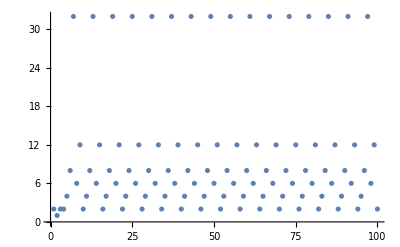

```mathematica
ListPlot[%413]
```

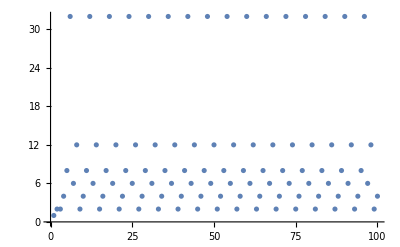

```mathematica
ListPlot[Table[full[i,1,2],{i, 1, 100}]]
```

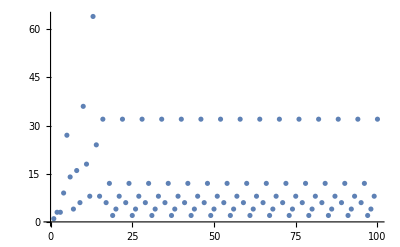

```mathematica
ListPlot[Table[full[i,1,3],{i, 1, 100}]]
```

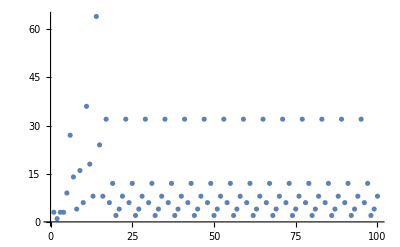

```mathematica
ListPlot[Table[full[i,3,1],{i, 1, 100}]]
```

```mathematica
Table[{j,k}->full[i,j,k],{i, 1, 10},{j,1,9},{k,1,9}]
```

{{{{1,1}→1,{1,2}→1,{1,3}→1,{1,4}→1,{1,5}→1,{1,6}→1,{1,7}→1,{1,8}→1,{1,9}→1},{{2,1}→2,{2,2}→2,{2,3}→2,{2,4}→2,{2,5}→2,{2,6}→2,{2,7}→2,{2,8}→2,{2,9}→2},{{3,1}→3,{3,2}→3,{3,3}→3,{3,4}→3,{3,5}→3,{3,6}→3,{3,7}→3,{3,8}→3,{3,9}→3},{{4,1}→4,{4,2}→4,{4,3}→4,{4,4}→4,{4,5}→4,{4,6}→4,{4,7}→4,{4,8}→4,{4,9}→4},{{5,1}→5,{5,2}→5,{5,3}→5,{5,4}→5,{5,5}→5,{5,6}→5,{5,7}→5,{5,8}→5,{5,9}→5},{{6,1}→6,{6,2}→6,{6,3}→6,{6,4}→6,{6,5}→6,{6,6}→6,{6,7}→6,{6,8}→6,{6,9}→6},{{7,1}→7,{7,2}→7,{7,3}→7,{7,4}→7,{7,5}→7,{7,6}→7,{7,7}→7,{7,8}→7,{7,9}→7},{{8,1}→8,{8,2}→8,{8,3}→8,{8,4}→8,{8,5}→8,{8,6}→8,{8,7}→8,{8,8}→8,{8,9}→8},{{9,1}→9,{9,2}→9,{9,3}→9,{9,4}→9,{9,5}→9,{9,6}→9,{9,7}→9,{9,8}→9,{9,9}→9}},{{{1,1}→1,{1,2}→2,{1,3}→3,{1,4}→4,{1,5}→5,{1,6}→6,{1,7}→7,{1,8}→8,{1,9}→9},{{2,1}→1,{2,2}→2,{2,3}→3,{2,4}→4,{2,5}→5,{2,6}→6,{2,7}→7,{2,8}→8,{2,9}→9},{{3,1}→1,{3,2}→2,{3,3}→3,{3,4}→4,{3,5}→5,{3,6}→6,{3,7}→7,{3,8}→8,{3,9}→9},{{4,1}→1,{4,2}→2,{4,3}→3,{4,4}→4,{4,5}→5,{4,6}→6,{4,7}→7,{4,8}→8,{4,9}→9},{{5,1}→1,{5,2}→2,{5,3}→3,{5,4}→4,{5,5}→5,{5,6}→6,{5,7}→7,{5,8}→8,{5,9}→9},{{6,1}→1,{6,2}→2,{6,3}→3,{6,4}→4,{6,5}→5,{6,6}→6,{6,7}→7,{6,8}→8,{6,9}→9},{{7,1}→1,{7,2}→2,{7,3}→3,{7,4}→4,{7,5}→5,{7,6}→6,{7,7}→7,{7,8}→8,{7,9}→9},{{8,1}→1,{8,2}→2,{8,3}→3,{8,4}→4,{8,5}→5,{8,6}→6,{8,7}→7,{8,8}→8,{8,9}→9},{{9,1}→1,{9,2}→2,{9,3}→3,{9,4}→4,{9,5}→5,{9,6}→6,{9,7}→7,{9,8}→8,{9,9}→9}},{{{1,1}→1,{1,2}→2,{1,3}→3,{1,4}→4,{1,5}→5,{1,6}→6,{1,7}→7,{1,8}→8,{1,9}→9},{{2,1}→2,{2,2}→4,{2,3}→6,{2,4}→8,{2,5}→10,{2,6}→12,{2,7}→14,{2,8}→16,{2,9}→18},{{3,1}→3,{3,2}→6,{3,3}→9,{3,4}→12,{3,5}→15,{3,6}→18,{3,7}→21,{3,8}→24,{3,9}→27},{{4,1}→4,{4,2}→8,{4,3}→12,{4,4}→16,{4,5}→20,{4,6}→24,{4,7}→28,{4,8}→32,{4,9}→36},{{5,1}→5,{5,2}→10,{5,3}→15,{5,4}→20,{5,5}→25,{5,6}→30,{5,7}→35,{5,8}→40,{5,9}→45},{{6,1}→6,{6,2}→12,{6,3}→18,{6,4}→24,{6,5}→30,{6,6}→36,{6,7}→42,{6,8}→48,{6,9}→54},{{7,1}→7,{7,2}→14,{7,3}→21,{7,4}→28,{7,5}→35,{7,6}→42,{7,7}→49,{7,8}→56,{7,9}→63},{{8,1}→8,{8,2}→16,{8,3}→24,{8,4}→32,{8,5}→40,{8,6}→48,{8,7}→56,{8,8}→64,{8,9}→72},{{9,1}→9,{9,2}→18,{9,3}→27,{9,4}→36,{9,5}→45,{9,6}→54,{9,7}→63,{9,8}→72,{9,9}→81}},{{{1,1}→1,{1,2}→4,{1,3}→9,{1,4}→16,{1,5}→25,{1,6}→36,{1,7}→49,{1,8}→64,{1,9}→81},{{2,1}→2,{2,2}→8,{2,3}→18,{2,4}→32,{2,5}→0,{2,6}→2,{2,7}→4,{2,8}→6,{2,9}→8},{{3,1}→3,{3,2}→12,{3,3}→27,{3,4}→2,{3,5}→5,{3,6}→8,{3,7}→2,{3,8}→8,{3,9}→14},{{4,1}→4,{4,2}→16,{4,3}→2,{4,4}→6,{4,5}→0,{4,6}→8,{4,7}→16,{4,8}→6,{4,9}→18},{{5,1}→5,{5,2}→0,{5,3}→5,{5,4}→0,{5,5}→10,{5,6}→0,{5,7}→15,{5,8}→0,{5,9}→20},{{6,1}→6,{6,2}→2,{6,3}→8,{6,4}→8,{6,5}→0,{6,6}→18,{6,7}→8,{6,8}→32,{6,9}→20},{{7,1}→7,{7,2}→4,{7,3}→2,{7,4}→16,{7,5}→15,{7,6}→8,{7,7}→36,{7,8}→30,{7,9}→18},{{8,1}→8,{8,2}→6,{8,3}→8,{8,4}→6,{8,5}→0,{8,6}→32,{8,7}→30,{8,8}→24,{8,9}→14},{{9,1}→9,{9,2}→8,{9,3}→14,{9,4}→18,{9,5}→20,{9,6}→20,{9,7}→18,{9,8}→14,{9,9}→8}},{{{1,1}→1,{1,2}→8,{1,3}→27,{1,4}→6,{1,5}→10,{1,6}→18,{1,7}→36,{1,8}→24,{1,9}→8},{{2,1}→4,{2,2}→32,{2,3}→8,{2,4}→6,{2,5}→0,{2,6}→4,{2,7}→16,{2,8}→36,{2,9}→64},{{3,1}→9,{3,2}→2,{3,3}→14,{3,4}→4,{3,5}→25,{3,6}→64,{3,7}→2,{3,8}→32,{3,9}→4},{{4,1}→16,{4,2}→6,{4,3}→4,{4,4}→36,{4,5}→0,{4,6}→32,{4,7}→6,{4,8}→12,{4,9}→8},{{5,1}→25,{5,2}→0,{5,3}→25,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→5,{5,8}→0,{5,9}→0},{{6,1}→36,{6,2}→4,{6,3}→64,{6,4}→32,{6,5}→0,{6,6}→8,{6,7}→16,{6,8}→6,{6,9}→0},{{7,1}→49,{7,2}→16,{7,3}→2,{7,4}→6,{7,5}→5,{7,6}→16,{7,7}→18,{7,8}→0,{7,9}→8},{{8,1}→64,{8,2}→36,{8,3}→32,{8,4}→12,{8,5}→0,{8,6}→6,{8,7}→0,{8,8}→8,{8,9}→4},{{9,1}→81,{9,2}→64,{9,3}→4,{9,4}→8,{9,5}→0,{9,6}→0,{9,7}→8,{9,8}→4,{9,9}→8}},{{{1,1}→1,{1,2}→32,{1,3}→14,{1,4}→36,{1,5}→0,{1,6}→8,{1,7}→18,{1,8}→8,{1,9}→8},{{2,1}→8,{2,2}→6,{2,3}→64,{2,4}→12,{2,5}→0,{2,6}→8,{2,7}→6,{2,8}→18,{2,9}→24},{{3,1}→27,{3,2}→4,{3,3}→4,{3,4}→8,{3,5}→10,{3,6}→24,{3,7}→4,{3,8}→6,{3,9}→16},{{4,1}→6,{4,2}→36,{4,3}→8,{4,4}→18,{4,5}→0,{4,6}→6,{4,7}→36,{4,8}→2,{4,9}→64},{{5,1}→10,{5,2}→0,{5,3}→10,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→25,{5,8}→0,{5,9}→0},{{6,1}→18,{6,2}→8,{6,3}→24,{6,4}→6,{6,5}→0,{6,6}→64,{6,7}→6,{6,8}→12,{6,9}→0},{{7,1}→36,{7,2}→6,{7,3}→4,{7,4}→36,{7,5}→25,{7,6}→6,{7,7}→8,{7,8}→0,{7,9}→64},{{8,1}→24,{8,2}→18,{8,3}→6,{8,4}→2,{8,5}→0,{8,6}→12,{8,7}→0,{8,8}→32,{8,9}→16},{{9,1}→8,{9,2}→24,{9,3}→16,{9,4}→64,{9,5}→0,{9,6}→0,{9,7}→64,{9,8}→16,{9,9}→64}},{{{1,1}→1,{1,2}→6,{1,3}→4,{1,4}→18,{1,5}→0,{1,6}→64,{1,7}→8,{1,8}→32,{1,9}→64},{{2,1}→32,{2,2}→12,{2,3}→24,{2,4}→2,{2,5}→0,{2,6}→32,{2,7}→36,{2,8}→8,{2,9}→8},{{3,1}→14,{3,2}→8,{3,3}→16,{3,4}→32,{3,5}→0,{3,6}→8,{3,7}→8,{3,8}→12,{3,9}→6},{{4,1}→36,{4,2}→18,{4,3}→32,{4,4}→8,{4,5}→0,{4,6}→12,{4,7}→18,{4,8}→4,{4,9}→24},{{5,1}→0,{5,2}→0,{5,3}→0,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→10,{5,8}→0,{5,9}→0},{{6,1}→8,{6,2}→32,{6,3}→8,{6,4}→12,{6,5}→0,{6,6}→24,{6,7}→36,{6,8}→2,{6,9}→0},{{7,1}→18,{7,2}→36,{7,3}→8,{7,4}→18,{7,5}→10,{7,6}→36,{7,7}→64,{7,8}→0,{7,9}→24},{{8,1}→8,{8,2}→8,{8,3}→12,{8,4}→4,{8,5}→0,{8,6}→2,{8,7}→0,{8,8}→6,{8,9}→6},{{9,1}→8,{9,2}→8,{9,3}→6,{9,4}→24,{9,5}→0,{9,6}→0,{9,7}→24,{9,8}→6,{9,9}→24}},{{{1,1}→1,{1,2}→12,{1,3}→16,{1,4}→8,{1,5}→0,{1,6}→24,{1,7}→64,{1,8}→6,{1,9}→24},{{2,1}→6,{2,2}→2,{2,3}→8,{2,4}→4,{2,5}→0,{2,6}→6,{2,7}→18,{2,8}→64,{2,9}→32},{{3,1}→4,{3,2}→32,{3,3}→6,{3,4}→6,{3,5}→0,{3,6}→32,{3,7}→32,{3,8}→2,{3,9}→36},{{4,1}→18,{4,2}→8,{4,3}→6,{4,4}→64,{4,5}→0,{4,6}→2,{4,7}→8,{4,8}→8,{4,9}→8},{{5,1}→0,{5,2}→0,{5,3}→0,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→0,{5,8}→0,{5,9}→0},{{6,1}→64,{6,2}→6,{6,3}→32,{6,4}→2,{6,5}→0,{6,6}→8,{6,7}→18,{6,8}→4,{6,9}→0},{{7,1}→8,{7,2}→18,{7,3}→32,{7,4}→8,{7,5}→0,{7,6}→18,{7,7}→24,{7,8}→0,{7,9}→8},{{8,1}→32,{8,2}→64,{8,3}→2,{8,4}→8,{8,5}→0,{8,6}→4,{8,7}→0,{8,8}→12,{8,9}→36},{{9,1}→64,{9,2}→32,{9,3}→36,{9,4}→8,{9,5}→0,{9,6}→0,{9,7}→8,{9,8}→36,{9,9}→8}},{{{1,1}→1,{1,2}→2,{1,3}→6,{1,4}→64,{1,5}→0,{1,6}→8,{1,7}→24,{1,8}→12,{1,9}→8},{{2,1}→12,{2,2}→4,{2,3}→32,{2,4}→8,{2,5}→0,{2,6}→12,{2,7}→8,{2,8}→24,{2,9}→6},{{3,1}→16,{3,2}→6,{3,3}→36,{3,4}→12,{3,5}→0,{3,6}→6,{3,7}→6,{3,8}→4,{3,9}→18},{{4,1}→8,{4,2}→64,{4,3}→12,{4,4}→24,{4,5}→0,{4,6}→4,{4,7}→64,{4,8}→32,{4,9}→32},{{5,1}→0,{5,2}→0,{5,3}→0,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→0,{5,8}→0,{5,9}→0},{{6,1}→24,{6,2}→12,{6,3}→6,{6,4}→4,{6,5}→0,{6,6}→32,{6,7}→8,{6,8}→8,{6,9}→0},{{7,1}→64,{7,2}→8,{7,3}→6,{7,4}→64,{7,5}→0,{7,6}→8,{7,7}→8,{7,8}→0,{7,9}→32},{{8,1}→6,{8,2}→24,{8,3}→4,{8,4}→32,{8,5}→0,{8,6}→8,{8,7}→0,{8,8}→2,{8,9}→18},{{9,1}→24,{9,2}→6,{9,3}→18,{9,4}→32,{9,5}→0,{9,6}→0,{9,7}→32,{9,8}→18,{9,9}→32}},{{{1,1}→1,{1,2}→4,{1,3}→36,{1,4}→24,{1,5}→0,{1,6}→32,{1,7}→8,{1,8}→2,{1,9}→32},{{2,1}→2,{2,2}→8,{2,3}→6,{2,4}→32,{2,5}→0,{2,6}→2,{2,7}→64,{2,8}→8,{2,9}→12},{{3,1}→6,{3,2}→12,{3,3}→18,{3,4}→2,{3,5}→0,{3,6}→12,{3,7}→12,{3,8}→8,{3,9}→8},{{4,1}→64,{4,2}→24,{4,3}→2,{4,4}→8,{4,5}→0,{4,6}→8,{4,7}→24,{4,8}→6,{4,9}→6},{{5,1}→0,{5,2}→0,{5,3}→0,{5,4}→0,{5,5}→0,{5,6}→0,{5,7}→0,{5,8}→0,{5,9}→0},{{6,1}→8,{6,2}→2,{6,3}→12,{6,4}→8,{6,5}→0,{6,6}→6,{6,7}→64,{6,8}→32,{6,9}→0},{{7,1}→24,{7,2}→64,{7,3}→12,{7,4}→24,{7,5}→0,{7,6}→64,{7,7}→32,{7,8}→0,{7,9}→6},{{8,1}→12,{8,2}→8,{8,3}→8,{8,4}→6,{8,5}→0,{8,6}→32,{8,7}→0,{8,8}→4,{8,9}→8},{{9,1}→8,{9,2}→12,{9,3}→8,{9,4}→6,{9,5}→0,{9,6}→0,{9,7}→6,{9,8}→8,{9,9}→6}}}

```mathematica
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 10}],
{j,1,9},{k,1,9}]
```

{{{1,1}→{1,1,1,1,1,1,1,1,1,1},{1,2}→{1,2,2,4,8,32,6,12,2,4},{1,3}→{1,3,3,9,27,14,4,16,6,36},{1,4}→{1,4,4,16,6,36,18,8,64,24},{1,5}→{1,5,5,25,10,0,0,0,0,0},{1,6}→{1,6,6,36,18,8,64,24,8,32},{1,7}→{1,7,7,49,36,18,8,64,24,8},{1,8}→{1,8,8,64,24,8,32,6,12,2},{1,9}→{1,9,9,81,8,8,64,24,8,32}},{{2,1}→{2,1,2,2,4,8,32,6,12,2},{2,2}→{2,2,4,8,32,6,12,2,4,8},{2,3}→{2,3,6,18,8,64,24,8,32,6},{2,4}→{2,4,8,32,6,12,2,4,8,32},{2,5}→{2,5,10,0,0,0,0,0,0,0},{2,6}→{2,6,12,2,4,8,32,6,12,2},{2,7}→{2,7,14,4,16,6,36,18,8,64},{2,8}→{2,8,16,6,36,18,8,64,24,8},{2,9}→{2,9,18,8,64,24,8,32,6,12}},{{3,1}→{3,1,3,3,9,27,14,4,16,6},{3,2}→{3,2,6,12,2,4,8,32,6,12},{3,3}→{3,3,9,27,14,4,16,6,36,18},{3,4}→{3,4,12,2,4,8,32,6,12,2},{3,5}→{3,5,15,5,25,10,0,0,0,0},{3,6}→{3,6,18,8,64,24,8,32,6,12},{3,7}→{3,7,21,2,2,4,8,32,6,12},{3,8}→{3,8,24,8,32,6,12,2,4,8},{3,9}→{3,9,27,14,4,16,6,36,18,8}},{{4,1}→{4,1,4,4,16,6,36,18,8,64},{4,2}→{4,2,8,16,6,36,18,8,64,24},{4,3}→{4,3,12,2,4,8,32,6,12,2},{4,4}→{4,4,16,6,36,18,8,64,24,8},{4,5}→{4,5,20,0,0,0,0,0,0,0},{4,6}→{4,6,24,8,32,6,12,2,4,8},{4,7}→{4,7,28,16,6,36,18,8,64,24},{4,8}→{4,8,32,6,12,2,4,8,32,6},{4,9}→{4,9,36,18,8,64,24,8,32,6}},{{5,1}→{5,1,5,5,25,10,0,0,0,0},{5,2}→{5,2,10,0,0,0,0,0,0,0},{5,3}→{5,3,15,5,25,10,0,0,0,0},{5,4}→{5,4,20,0,0,0,0,0,0,0},{5,5}→{5,5,25,10,0,0,0,0,0,0},{5,6}→{5,6,30,0,0,0,0,0,0,0},{5,7}→{5,7,35,15,5,25,10,0,0,0},{5,8}→{5,8,40,0,0,0,0,0,0,0},{5,9}→{5,9,45,20,0,0,0,0,0,0}},{{6,1}→{6,1,6,6,36,18,8,64,24,8},{6,2}→{6,2,12,2,4,8,32,6,12,2},{6,3}→{6,3,18,8,64,24,8,32,6,12},{6,4}→{6,4,24,8,32,6,12,2,4,8},{6,5}→{6,5,30,0,0,0,0,0,0,0},{6,6}→{6,6,36,18,8,64,24,8,32,6},{6,7}→{6,7,42,8,16,6,36,18,8,64},{6,8}→{6,8,48,32,6,12,2,4,8,32},{6,9}→{6,9,54,20,0,0,0,0,0,0}},{{7,1}→{7,1,7,7,49,36,18,8,64,24},{7,2}→{7,2,14,4,16,6,36,18,8,64},{7,3}→{7,3,21,2,2,4,8,32,6,12},{7,4}→{7,4,28,16,6,36,18,8,64,24},{7,5}→{7,5,35,15,5,25,10,0,0,0},{7,6}→{7,6,42,8,16,6,36,18,8,64},{7,7}→{7,7,49,36,18,8,64,24,8,32},{7,8}→{7,8,56,30,0,0,0,0,0,0},{7,9}→{7,9,63,18,8,64,24,8,32,6}},{{8,1}→{8,1,8,8,64,24,8,32,6,12},{8,2}→{8,2,16,6,36,18,8,64,24,8},{8,3}→{8,3,24,8,32,6,12,2,4,8},{8,4}→{8,4,32,6,12,2,4,8,32,6},{8,5}→{8,5,40,0,0,0,0,0,0,0},{8,6}→{8,6,48,32,6,12,2,4,8,32},{8,7}→{8,7,56,30,0,0,0,0,0,0},{8,8}→{8,8,64,24,8,32,6,12,2,4},{8,9}→{8,9,72,14,4,16,6,36,18,8}},{{9,1}→{9,1,9,9,81,8,8,64,24,8},{9,2}→{9,2,18,8,64,24,8,32,6,12},{9,3}→{9,3,27,14,4,16,6,36,18,8},{9,4}→{9,4,36,18,8,64,24,8,32,6},{9,5}→{9,5,45,20,0,0,0,0,0,0},{9,6}→{9,6,54,20,0,0,0,0,0,0},{9,7}→{9,7,63,18,8,64,24,8,32,6},{9,8}→{9,8,72,14,4,16,6,36,18,8},{9,9}→{9,9,81,8,8,64,24,8,32,6}}}

```mathematica
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 15}],
{j,1,9},{k,1,9}]
```

{{{1,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,2}→{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2},{1,3}→{1,3,3,9,27,14,4,16,6,36,18,8,64,24,8},{1,4}→{1,4,4,16,6,36,18,8,64,24,8,32,6,12,2},{1,5}→{1,5,5,25,10,0,0,0,0,0,0,0,0,0,0},{1,6}→{1,6,6,36,18,8,64,24,8,32,6,12,2,4,8},{1,7}→{1,7,7,49,36,18,8,64,24,8,32,6,12,2,4},{1,8}→{1,8,8,64,24,8,32,6,12,2,4,8,32,6,12},{1,9}→{1,9,9,81,8,8,64,24,8,32,6,12,2,4,8}},{{2,1}→{2,1,2,2,4,8,32,6,12,2,4,8,32,6,12},{2,2}→{2,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{2,3}→{2,3,6,18,8,64,24,8,32,6,12,2,4,8,32},{2,4}→{2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{2,5}→{2,5,10,0,0,0,0,0,0,0,0,0,0,0,0},{2,6}→{2,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{2,7}→{2,7,14,4,16,6,36,18,8,64,24,8,32,6,12},{2,8}→{2,8,16,6,36,18,8,64,24,8,32,6,12,2,4},{2,9}→{2,9,18,8,64,24,8,32,6,12,2,4,8,32,6}},{{3,1}→{3,1,3,3,9,27,14,4,16,6,36,18,8,64,24},{3,2}→{3,2,6,12,2,4,8,32,6,12,2,4,8,32,6},{3,3}→{3,3,9,27,14,4,16,6,36,18,8,64,24,8,32},{3,4}→{3,4,12,2,4,8,32,6,12,2,4,8,32,6,12},{3,5}→{3,5,15,5,25,10,0,0,0,0,0,0,0,0,0},{3,6}→{3,6,18,8,64,24,8,32,6,12,2,4,8,32,6},{3,7}→{3,7,21,2,2,4,8,32,6,12,2,4,8,32,6},{3,8}→{3,8,24,8,32,6,12,2,4,8,32,6,12,2,4},{3,9}→{3,9,27,14,4,16,6,36,18,8,64,24,8,32,6}},{{4,1}→{4,1,4,4,16,6,36,18,8,64,24,8,32,6,12},{4,2}→{4,2,8,16,6,36,18,8,64,24,8,32,6,12,2},{4,3}→{4,3,12,2,4,8,32,6,12,2,4,8,32,6,12},{4,4}→{4,4,16,6,36,18,8,64,24,8,32,6,12,2,4},{4,5}→{4,5,20,0,0,0,0,0,0,0,0,0,0,0,0},{4,6}→{4,6,24,8,32,6,12,2,4,8,32,6,12,2,4},{4,7}→{4,7,28,16,6,36,18,8,64,24,8,32,6,12,2},{4,8}→{4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{4,9}→{4,9,36,18,8,64,24,8,32,6,12,2,4,8,32}},{{5,1}→{5,1,5,5,25,10,0,0,0,0,0,0,0,0,0},{5,2}→{5,2,10,0,0,0,0,0,0,0,0,0,0,0,0},{5,3}→{5,3,15,5,25,10,0,0,0,0,0,0,0,0,0},{5,4}→{5,4,20,0,0,0,0,0,0,0,0,0,0,0,0},{5,5}→{5,5,25,10,0,0,0,0,0,0,0,0,0,0,0},{5,6}→{5,6,30,0,0,0,0,0,0,0,0,0,0,0,0},{5,7}→{5,7,35,15,5,25,10,0,0,0,0,0,0,0,0},{5,8}→{5,8,40,0,0,0,0,0,0,0,0,0,0,0,0},{5,9}→{5,9,45,20,0,0,0,0,0,0,0,0,0,0,0}},{{6,1}→{6,1,6,6,36,18,8,64,24,8,32,6,12,2,4},{6,2}→{6,2,12,2,4,8,32,6,12,2,4,8,32,6,12},{6,3}→{6,3,18,8,64,24,8,32,6,12,2,4,8,32,6},{6,4}→{6,4,24,8,32,6,12,2,4,8,32,6,12,2,4},{6,5}→{6,5,30,0,0,0,0,0,0,0,0,0,0,0,0},{6,6}→{6,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{6,7}→{6,7,42,8,16,6,36,18,8,64,24,8,32,6,12},{6,8}→{6,8,48,32,6,12,2,4,8,32,6,12,2,4,8},{6,9}→{6,9,54,20,0,0,0,0,0,0,0,0,0,0,0}},{{7,1}→{7,1,7,7,49,36,18,8,64,24,8,32,6,12,2},{7,2}→{7,2,14,4,16,6,36,18,8,64,24,8,32,6,12},{7,3}→{7,3,21,2,2,4,8,32,6,12,2,4,8,32,6},{7,4}→{7,4,28,16,6,36,18,8,64,24,8,32,6,12,2},{7,5}→{7,5,35,15,5,25,10,0,0,0,0,0,0,0,0},{7,6}→{7,6,42,8,16,6,36,18,8,64,24,8,32,6,12},{7,7}→{7,7,49,36,18,8,64,24,8,32,6,12,2,4,8},{7,8}→{7,8,56,30,0,0,0,0,0,0,0,0,0,0,0},{7,9}→{7,9,63,18,8,64,24,8,32,6,12,2,4,8,32}},{{8,1}→{8,1,8,8,64,24,8,32,6,12,2,4,8,32,6},{8,2}→{8,2,16,6,36,18,8,64,24,8,32,6,12,2,4},{8,3}→{8,3,24,8,32,6,12,2,4,8,32,6,12,2,4},{8,4}→{8,4,32,6,12,2,4,8,32,6,12,2,4,8,32},{8,5}→{8,5,40,0,0,0,0,0,0,0,0,0,0,0,0},{8,6}→{8,6,48,32,6,12,2,4,8,32,6,12,2,4,8},{8,7}→{8,7,56,30,0,0,0,0,0,0,0,0,0,0,0},{8,8}→{8,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{8,9}→{8,9,72,14,4,16,6,36,18,8,64,24,8,32,6}},{{9,1}→{9,1,9,9,81,8,8,64,24,8,32,6,12,2,4},{9,2}→{9,2,18,8,64,24,8,32,6,12,2,4,8,32,6},{9,3}→{9,3,27,14,4,16,6,36,18,8,64,24,8,32,6},{9,4}→{9,4,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,5}→{9,5,45,20,0,0,0,0,0,0,0,0,0,0,0},{9,6}→{9,6,54,20,0,0,0,0,0,0,0,0,0,0,0},{9,7}→{9,7,63,18,8,64,24,8,32,6,12,2,4,8,32},{9,8}→{9,8,72,14,4,16,6,36,18,8,64,24,8,32,6},{9,9}→{9,9,81,8,8,64,24,8,32,6,12,2,4,8,32}}}

```mathematica
Flatten[
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 15}],
{j,1,9},{k,1,9}],1]
```

{{1,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,2}→{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2},{1,3}→{1,3,3,9,27,14,4,16,6,36,18,8,64,24,8},{1,4}→{1,4,4,16,6,36,18,8,64,24,8,32,6,12,2},{1,5}→{1,5,5,25,10,0,0,0,0,0,0,0,0,0,0},{1,6}→{1,6,6,36,18,8,64,24,8,32,6,12,2,4,8},{1,7}→{1,7,7,49,36,18,8,64,24,8,32,6,12,2,4},{1,8}→{1,8,8,64,24,8,32,6,12,2,4,8,32,6,12},{1,9}→{1,9,9,81,8,8,64,24,8,32,6,12,2,4,8},{2,1}→{2,1,2,2,4,8,32,6,12,2,4,8,32,6,12},{2,2}→{2,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{2,3}→{2,3,6,18,8,64,24,8,32,6,12,2,4,8,32},{2,4}→{2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{2,5}→{2,5,10,0,0,0,0,0,0,0,0,0,0,0,0},{2,6}→{2,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{2,7}→{2,7,14,4,16,6,36,18,8,64,24,8,32,6,12},{2,8}→{2,8,16,6,36,18,8,64,24,8,32,6,12,2,4},{2,9}→{2,9,18,8,64,24,8,32,6,12,2,4,8,32,6},{3,1}→{3,1,3,3,9,27,14,4,16,6,36,18,8,64,24},{3,2}→{3,2,6,12,2,4,8,32,6,12,2,4,8,32,6},{3,3}→{3,3,9,27,14,4,16,6,36,18,8,64,24,8,32},{3,4}→{3,4,12,2,4,8,32,6,12,2,4,8,32,6,12},{3,5}→{3,5,15,5,25,10,0,0,0,0,0,0,0,0,0},{3,6}→{3,6,18,8,64,24,8,32,6,12,2,4,8,32,6},{3,7}→{3,7,21,2,2,4,8,32,6,12,2,4,8,32,6},{3,8}→{3,8,24,8,32,6,12,2,4,8,32,6,12,2,4},{3,9}→{3,9,27,14,4,16,6,36,18,8,64,24,8,32,6},{4,1}→{4,1,4,4,16,6,36,18,8,64,24,8,32,6,12},{4,2}→{4,2,8,16,6,36,18,8,64,24,8,32,6,12,2},{4,3}→{4,3,12,2,4,8,32,6,12,2,4,8,32,6,12},{4,4}→{4,4,16,6,36,18,8,64,24,8,32,6,12,2,4},{4,5}→{4,5,20,0,0,0,0,0,0,0,0,0,0,0,0},{4,6}→{4,6,24,8,32,6,12,2,4,8,32,6,12,2,4},{4,7}→{4,7,28,16,6,36,18,8,64,24,8,32,6,12,2},{4,8}→{4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{4,9}→{4,9,36,18,8,64,24,8,32,6,12,2,4,8,32},{5,1}→{5,1,5,5,25,10,0,0,0,0,0,0,0,0,0},{5,2}→{5,2,10,0,0,0,0,0,0,0,0,0,0,0,0},{5,3}→{5,3,15,5,25,10,0,0,0,0,0,0,0,0,0},{5,4}→{5,4,20,0,0,0,0,0,0,0,0,0,0,0,0},{5,5}→{5,5,25,10,0,0,0,0,0,0,0,0,0,0,0},{5,6}→{5,6,30,0,0,0,0,0,0,0,0,0,0,0,0},{5,7}→{5,7,35,15,5,25,10,0,0,0,0,0,0,0,0},{5,8}→{5,8,40,0,0,0,0,0,0,0,0,0,0,0,0},{5,9}→{5,9,45,20,0,0,0,0,0,0,0,0,0,0,0},{6,1}→{6,1,6,6,36,18,8,64,24,8,32,6,12,2,4},{6,2}→{6,2,12,2,4,8,32,6,12,2,4,8,32,6,12},{6,3}→{6,3,18,8,64,24,8,32,6,12,2,4,8,32,6},{6,4}→{6,4,24,8,32,6,12,2,4,8,32,6,12,2,4},{6,5}→{6,5,30,0,0,0,0,0,0,0,0,0,0,0,0},{6,6}→{6,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{6,7}→{6,7,42,8,16,6,36,18,8,64,24,8,32,6,12},{6,8}→{6,8,48,32,6,12,2,4,8,32,6,12,2,4,8},{6,9}→{6,9,54,20,0,0,0,0,0,0,0,0,0,0,0},{7,1}→{7,1,7,7,49,36,18,8,64,24,8,32,6,12,2},{7,2}→{7,2,14,4,16,6,36,18,8,64,24,8,32,6,12},{7,3}→{7,3,21,2,2,4,8,32,6,12,2,4,8,32,6},{7,4}→{7,4,28,16,6,36,18,8,64,24,8,32,6,12,2},{7,5}→{7,5,35,15,5,25,10,0,0,0,0,0,0,0,0},{7,6}→{7,6,42,8,16,6,36,18,8,64,24,8,32,6,12},{7,7}→{7,7,49,36,18,8,64,24,8,32,6,12,2,4,8},{7,8}→{7,8,56,30,0,0,0,0,0,0,0,0,0,0,0},{7,9}→{7,9,63,18,8,64,24,8,32,6,12,2,4,8,32},{8,1}→{8,1,8,8,64,24,8,32,6,12,2,4,8,32,6},{8,2}→{8,2,16,6,36,18,8,64,24,8,32,6,12,2,4},{8,3}→{8,3,24,8,32,6,12,2,4,8,32,6,12,2,4},{8,4}→{8,4,32,6,12,2,4,8,32,6,12,2,4,8,32},{8,5}→{8,5,40,0,0,0,0,0,0,0,0,0,0,0,0},{8,6}→{8,6,48,32,6,12,2,4,8,32,6,12,2,4,8},{8,7}→{8,7,56,30,0,0,0,0,0,0,0,0,0,0,0},{8,8}→{8,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{8,9}→{8,9,72,14,4,16,6,36,18,8,64,24,8,32,6},{9,1}→{9,1,9,9,81,8,8,64,24,8,32,6,12,2,4},{9,2}→{9,2,18,8,64,24,8,32,6,12,2,4,8,32,6},{9,3}→{9,3,27,14,4,16,6,36,18,8,64,24,8,32,6},{9,4}→{9,4,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,5}→{9,5,45,20,0,0,0,0,0,0,0,0,0,0,0},{9,6}→{9,6,54,20,0,0,0,0,0,0,0,0,0,0,0},{9,7}→{9,7,63,18,8,64,24,8,32,6,12,2,4,8,32},{9,8}→{9,8,72,14,4,16,6,36,18,8,64,24,8,32,6},{9,9}→{9,9,81,8,8,64,24,8,32,6,12,2,4,8,32}}

```mathematica
Flatten[
Table[
{j,k}->
Table[full[i,j,k], {i, 1, 20}],
{j,1,9},{k,1,9}],1]
```

{{1,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,2}→{1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{1,3}→{1,3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4},{1,4}→{1,4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{1,5}→{1,5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,6}→{1,6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{1,7}→{1,7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{1,8}→{1,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{1,9}→{1,9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{2,1}→{2,1,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{2,2}→{2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{2,3}→{2,3,6,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{2,4}→{2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{2,5}→{2,5,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,6}→{2,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{2,7}→{2,7,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{2,8}→{2,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{2,9}→{2,9,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,1}→{3,1,3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2},{3,2}→{3,2,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,3}→{3,3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8},{3,4}→{3,4,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{3,5}→{3,5,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3,6}→{3,6,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,7}→{3,7,21,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{3,8}→{3,8,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{3,9}→{3,9,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{4,1}→{4,1,4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{4,2}→{4,2,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{4,3}→{4,3,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{4,4}→{4,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{4,5}→{4,5,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{4,6}→{4,6,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{4,7}→{4,7,28,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{4,8}→{4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{4,9}→{4,9,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{5,1}→{5,1,5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,2}→{5,2,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,3}→{5,3,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,4}→{5,4,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,5}→{5,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,6}→{5,6,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,7}→{5,7,35,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,8}→{5,8,40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{5,9}→{5,9,45,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,1}→{6,1,6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{6,2}→{6,2,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6},{6,3}→{6,3,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{6,4}→{6,4,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{6,5}→{6,5,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6,6}→{6,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{6,7}→{6,7,42,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{6,8}→{6,8,48,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{6,9}→{6,9,54,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,1}→{7,1,7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{7,2}→{7,2,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{7,3}→{7,3,21,2,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{7,4}→{7,4,28,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12},{7,5}→{7,5,35,15,5,25,10,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,6}→{7,6,42,8,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6},{7,7}→{7,7,49,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4},{7,8}→{7,8,56,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,9}→{7,9,63,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{8,1}→{8,1,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{8,2}→{8,2,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{8,3}→{8,3,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2},{8,4}→{8,4,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4,8},{8,5}→{8,5,40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,6}→{8,6,48,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12,2,4},{8,7}→{8,7,56,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{8,8}→{8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32,6,12},{8,9}→{8,9,72,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,1}→{9,1,9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2},{9,2}→{9,2,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8,32},{9,3}→{9,3,27,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,4}→{9,4,36,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{9,5}→{9,5,45,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,6}→{9,6,54,20,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{9,7}→{9,7,63,18,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8},{9,8}→{9,8,72,14,4,16,6,36,18,8,64,24,8,32,6,12,2,4,8,32},{9,9}→{9,9,81,8,8,64,24,8,32,6,12,2,4,8,32,6,12,2,4,8}}

```mathematica
LinguisticAssistant
```